#### A two-host, environmental-transmission model

This model assumes environmental transmission, but where the parasite actively seeks out hosts. Contact is thus controlled by the parasite (so β_i can quantify both the contact and infection processes), and contact is assumed to remove parasites from the environment. I will assume that the resident parasite strain exploits a single host and ask whether a mutant that can exploit both hosts can invade if “generalism” comes at a cost of reducing the shedding rate from both hosts. Let the parameter a quantify the cost of generalism. I will let K_1 and K_2 be the carrying capacities of the first host and second host; similarly, μ_1 and μ_2 will be the mortality rates of hosts 1 and 2 and λ_1 and λ_2 will be the shedding rates from hosts 1 and 2. Technically, under this model, K is not properly described as a carrying capacity, since the actual equilibrium abundance is actually K_1(1-μ_1/r_1). For simplicity, I will assume that all other parameters (traits) are equal between the hosts and parasites.

```mathematica
dS1dt=r1 (S1+I1r+I1m) (1-(S1+I1r+I1m)/K1)-β S1 (Pr+Pm);
dS2dt=r2 (S2+I2m) (1-(S2+I2m)/K2)-β S2 (Pr+Pm);
dI1rdt=β S1 Pr-μ1 I1r;
dPrdt=λ1 I1r-β S1 Pr-γ Pr;
dI1mdt=β S1 Pm-μ1 I1m;
dI2mdt=β S2 Pm-μ2 I2m;
dPmdt=a λ1 I1m+a λ2 I2m-β S1 Pm-β S2 Pm-γ Pm;
```

For an invasion analysis, we assume that the resident parasite comes to an ecological equilibrium with the host. Since it does not parasitize the second host, it will go to its carrying capacity: S_2=K_2. The density of the exploited host at equilibrium will be S_1=(γ μ_1)/(β (λ_1-μ_1)).

```mathematica
Eq=Solve[({dS1dt==0,dI1rdt==0,dPrdt==0}/.{I1m->0,Pm->0}),{S1,I1r,Pr}];
Eq[[1;;4,1]]
```

{S1→0,S1→K1,S1→-(γ μ1)/(β (-λ1+μ1)),S1→-(γ μ1)/(β (-λ1+μ1))}

While evaluating the stability of the endemic equilibrium is somewhat challenging, it is obvious that, for there to be any chance for the endemic parasite equilibrium to be stable, the parasite extinction equilibrium must be unstable. This requires (β K (λ_1-μ))/(γ μ)>1. Notice that this is the reciprocal of the equilibrium host abundance at the endemic equilibrium, as expected.

```mathematica
Jres={{D[dS1dt,S1],D[dS1dt,I1r],D[dS1dt,Pr]},
{D[dI1rdt,S1],D[dI1rdt,I1r],D[dI1rdt,Pr]},
{D[dPrdt,S1],D[dPrdt,I1r],D[dPrdt,Pr]}}/.{I1m->0,Pm->0};
(* Eigenvalues for the parasite-free equilibrium *)
Eigenvalues[Jres/.{I1r->0,Pr->0,S1->K1}]
```

{-r1,1/2 (-K1 β-γ-μ1-√((K1 β+γ+μ1)^2-4 (-K1 β λ1+K1 β μ1+γ μ1))),1/2 (-K1 β-γ-μ1+√((K1 β+γ+μ1)^2-4 (-K1 β λ1+K1 β μ1+γ μ1)))}

We can calculate the invasion criterion from the rows and columns of the Jacobian dealing with the mutant parasite alone:

```mathematica
J={{D[dS1dt,S1],D[dS1dt,S2],D[dS1dt,I1r],D[dS1dt,Pr],D[dS1dt,I1m],D[dS1dt,I2m],D[dS1dt,Pm]},
{D[dS2dt,S1],D[dS2dt,S2],D[dS2dt,I1r],D[dS2dt,Pr],D[dS2dt,I1m],D[dS2dt,I2m],D[dS2dt,Pm]},
{D[dI1rdt,S1],D[dI1rdt,S2],D[dI1rdt,I1r],D[dI1rdt,Pr],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,Pm]},
{D[dPrdt,S1],D[dPrdt,S2],D[dPrdt,I1r],D[dPrdt,Pr],D[dPrdt,I1m],D[dPrdt,I2m],D[dPrdt,Pm]},
{D[dI1mdt,S1],D[dI1mdt,S2],D[dI1mdt,I1r],D[dI1mdt,Pr],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,Pm]},
{D[dI2mdt,S1],D[dI2mdt,S2],D[dI2mdt,I1r],D[dI2mdt,Pr],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,Pm]},
{D[dPmdt,S1],D[dPmdt,S2],D[dPmdt,I1r],D[dPmdt,Pr],D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,Pm]}}/.{I1m->0,I2m->0,Pm->0};
MatrixForm[J]
(* The eigenvalues of this matrix determine whether the mutant parasite can invade *)
MatrixForm[J[[5;;7,5;;7]]]
```

(-(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1)-Pr β | 0 | -(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1) | -S1 β | -(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1) | 0 | -S1 β
0 | -(r2 S2)/K2+r2 (1-S2/K2)-Pr β | 0 | -S2 β | 0 | -(r2 S2)/K2+r2 (1-S2/K2) | -S2 β
Pr β | 0 | -μ1 | S1 β | 0 | 0 | 0
-Pr β | 0 | λ1 | -S1 β-γ | 0 | 0 | 0
0 | 0 | 0 | 0 | -μ1 | 0 | S1 β
0 | 0 | 0 | 0 | 0 | -μ2 | S2 β
0 | 0 | 0 | 0 | a λ1 | a λ2 | -S1 β-S2 β-γ)

(-μ1 | 0 | S1 β
0 | -μ2 | S2 β
a λ1 | a λ2 | -S1 β-S2 β-γ)

Rather than look at those eigenvalues (which are difficult to interpret), it is easier to apply the next generation theorem.

```mathematica
F={{0,0,S1 β},{0,0,S2 β},{a λ1,a λ2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,S1 β+S2 β+γ}};
Simplify[Dot[F,Inverse[V]]];
Eigenvalues[Dot[F,Inverse[V]]]
```

{0,-(√a √β √(S2 λ2 μ1+S1 λ1 μ2))/(√(S1 β+S2 β+γ) √μ1 √μ2),(√a √β √(S2 λ2 μ1+S1 λ1 μ2))/(√(S1 β+S2 β+γ) √μ1 √μ2)}

Invasion requires 
(a λ β (μ_1 S_2+μ_2 S_1))/(μ_1 μ_2(β S_1+β S_2+γ))>1, which is equivalent to requiring that (β (a λ_1-μ_1))/(γ μ_1)S_1+(β (a λ_1-μ_2))/(γ μ_2)S_2>1.

```mathematica
a β λ (S2 μ1+S1 μ2)>(S1 β+S2 β+γ) μ1 μ2;
a S2 β λ μ1+a S1 β λ μ2>S1 β μ1 μ2+S2 β μ1 μ2+γ μ1 μ2;
β S2 μ1 (a λ-μ2)+β S1 μ2 (a λ-μ1)>γ μ1 μ2;
(β (a λ-μ1))/(γ μ1)S1+(β (a λ-μ2))/(γ μ2)S2>1;
```

Define invasion fitness as:

```mathematica
InvFit=((β (a λ1-μ1))/(γ μ1)S1+(β (a λ2-μ2))/(γ μ2)S2)/.{Eq[[3,1]],S2->K2 }
```

-(a λ1-μ1)/(-λ1+μ1)+(K2 β (a λ2-μ2))/(γ μ2)

Notice that both a λ_1-μ_1>0 and a λ_2-μ_2>0 for invasion to be possible. This is because, by assumption, a λ_1-μ_1>a λ_2-μ_2. If a λ_1-μ_1<0, then invasion fitness is obviously negative. If a λ_1-μ_1>0 but a λ_2-μ_2<0, invasion fitness will be less than 1: (a λ_1-μ_1)/(λ_1-μ_1)<1 because a<1, so if the second term of invasion fitness is negative, the entire expression must be less than one.

What is the effect of increasing a on the invasion fitness?

```mathematica
D[InvFit,a]
```

-λ1/(-λ1+μ1)+(K2 β λ2)/(γ μ2)

What is the effect of increasing K_2 on the invasion fitness?

```mathematica
D[InvFit,K2]
```

(β (a λ2-μ2))/(γ μ2)

What is the effect of increasing μ on the invasion fitness?

```mathematica
Simplify[D[InvFit,μ1]]
FullSimplify[D[InvFit,μ2]]
```

((-1+a) λ1)/(λ1-μ1)^2

-(a K2 β λ2)/(γ μ2^2)

What is the effect of increasing γ on the invasion fitness?

```mathematica
D[InvFit,γ]
```

-(K2 β (a λ2-μ2))/(γ^2 μ2)

#### Effect of body size

We can incorporate body size of the two hosts into the model in a fairly simple way. In particular, assume that birth rate, carrying capacity and mortality rate scale with body size and temperature according to (Savage 2004)
r=r_0 e^(-E/k T)W^-0.25
K=K_0 e^(E/k T)W^-0.75
μ = μ_0 e^(-E/k T)W^-0.25
Notice that this form implies that birth and mortality rates increase as temperature increases and decrease as mass increases, whereas carrying capacity decreases with both an increase in temperature and an increase in mass. This will be important later.

However, because within-host (or on-host, for ectoparasites) abundance also correlates with body size in an allometric way. If we assume that shedding rate is a linear function of abundance, we have a fourth allometric scaling. 
λ = λ_0 e^(-E/k T)W^0.75 (for endoparasites)
λ = λ_0 e^(-E/k T)W^(5/12) (for ectoparasites)

Note that the derivatives of these expressions can be rewritten in terms of the expressions themselves:

```mathematica
K2=K0 Exp[Ε/(k T)] (f W)^(-3/4);
μ1=μ0 Exp[-Ε/(k T)] W^(-1/4);
μ2=μ0 Exp[-Ε/(k T)] (f W)^(-1/4);
λ1=λ0 Exp[-Ε/(k T)] W^(3/4);
λ2=λ0 Exp[-Ε/(k T)] (f W)^(3/4);
r2=r0 Exp[-Ε/(k T)] (f W)^(-1/4);
D[μ1,W]==-μ1/(4 W)//Simplify
D[λ1,W]==(3 λ1)/(4 W)//Simplify
D[K2,W]==(-3 K2)/(4 W)//Simplify
D[μ2,W]==-μ2/(4 W)//Simplify
D[λ2,W]==(3 λ2)/(4 W)//Simplify
Clear[r2,μ2,K2,λ2,μ1,λ1]
```

True

True

True

«2 more identical outputs»

The invasion fitness in terms of W is:

```mathematica
InvFitW=-(a λ1[W]-μ1[W])/(-λ1[W]+μ1[W])+(K2[W]  β (a λ2[W]-μ2[W]))/(γ μ2[W]);
```

The derivative of the first term of the invasion fitness expression, with respect to mass W, can be written as

```mathematica
Simplify[D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W)}]
```

-((-1+a) λ1[W] μ1[W])/(W (λ1[W]-μ1[W])^2)

The derivative of the second term of the invasion fitness expression, with respect to mass W, can be expressed as

```mathematica
D[(K2[W] (1-μ0/r0) β (a λ2[W]-μ2[W]))/(γ μ2[W]),W]/.{K2'[W]->(-3 K2[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)}//Simplify
```

(β (r0-μ0) K2[W] (a λ2[W]+3 μ2[W]))/(4 r0 W γ μ2[W])

Thus, we can rewrite the derivative of invasion fitness with respect to size as:

```mathematica
(D[InvFitW,W]/.{μ1'[W]->(-μ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)})==((1-a) λ1[W] μ1[W])/(W (λ1[W]-μ1[W])^2)+(β K2[W] (a λ2[W]+3 μ2[W]))/(4 W γ μ2[W])//Simplify
```

True

Notice that because f occurs only in the second term of invasion fitness (dealing with infection in the secondary host), it is clear that the derivative of invasion fitness with respect to f must also be positive.

```mathematica
InvFitf=-(a λ1[W]-μ1[W])/(-λ1[W]+μ1[W])+(K2[f] β (a λ2[f]-μ2[f]))/(γ μ2[f]);
Simplify[D[InvFitf,f]/.{μ2'[f]->(-μ2[f])/(4 f),K2'[f]->(-3 K2[f])/(4 f),λ2'[f]->(3 λ2[f])/(4 f)}]
```

(β K2[f] (a λ2[f]+3 μ2[f]))/(4 f γ μ2[f])

With respect to temperature, the first term actually has a derivative of zero because both λ and μ scale with temperature in the same way. That is, both shedding rate and mortality rate increase at the same magnitude with an increase in temperature.

```mathematica
μ1=μ0 Exp[-Ε/(k T)] W^(-1/4);
λ1=λ0 Exp[-Ε/(k T)] W^(3/4);
D[μ1,T]==Ε/(k T^2)μ1//Simplify
D[λ1,T]==Ε/(k T^2)λ1//Simplify
Clear[μ1,λ1]
Simplify[D[(a λ1[T]-μ1[T])/(λ1[T]-μ1[T]),T]/.{μ1'[T]->Ε/(k T^2)μ1[T],λ1'[T]->Ε/(k T^2)λ1[T]}]
```

True

True

0

The second term is guaranteed to decrease with any increase in temperature.

```mathematica
K2=K0 Exp[Ε/(k T)] (f W)^(-3/4);
D[K2,T]==-Ε/(k T^2)K2//Simplify
Clear[K2]
D[(K2[T] (1-μ0/r0) β (a λ2[T]-μ2[T]))/(γ μ2[T]),T]/.{K2'[T]->-Ε/(k T^2)K2[T],μ2'[T]->Ε/(k T^2)μ2[T],λ2'[T]->Ε/(k T^2)λ2[T]}//Simplify
```

True

(β Ε (r0-μ0) K2[T] (-a λ2[T]+μ2[T]))/(k r0 T^2 γ μ2[T])

We can also look at the derivative of invasion fitness as both mass and temperature increase. This is negative, meaning that

```mathematica
D[(K2[W,T] β (a λ2[W,T]-μ2[W,T]))/(γ μ2[W,T]),W,T]/.{Derivative[0,1][K2][W,T]->-Ε/(k T^2)K2[W,T],Derivative[0,1][μ2][W,T]->Ε/(k T^2)μ2[W,T],Derivative[0,1][λ2][W,T]->Ε/(k T^2)λ2[W,T],
Derivative[1,0][μ2][W,T]->(-μ2[W,T])/(4 W),Derivative[1,0][K2][W,T]->(-3 K2[W,T])/(4 W),Derivative[1,0][λ2][W,T]->(3 λ2[W,T])/(4 W),Derivative[1,1][K2][W,T]->Ε/(k T^2)(3 K2[W,T])/(4 W),Derivative[1,1][μ2][W,T]->-Ε/(k T^2)μ2[W,T]/(4 W),Derivative[1,1][λ2][W,T]->Ε/(k T^2)(3 λ2[W,T])/(4 W)}//Simplify
```

```mathematica
-(β Ε K2[W,T] (a λ2[W,T]+3 μ2[W,T]))/(4 k T^2 W γ μ2[W,T])
InvFit
```

-(β Ε K2[W,T] (a λ2[W,T]+3 μ2[W,T]))/(4 k T^2 W γ μ2[W,T])

InvFit

```mathematica
μ1=Q2 Exp[-Ε/(k T)] W^(-1/4);
λ1=Q3 Exp[-Ε/(k T)] W^(3/4);
μ2=Q2 Exp[-Ε/(1.1 k T)] (1.1 W)^(-1/4);
λ2=Q3 Exp[-Ε/(1.1 k T)] (1.1 W)^(3/4);
(* First term of R0 expression *)
(* If you increase W and temperature by 10% does the magnitude of this term increase or decrease *)
Expand[Numerator[Simplify[((a λ1-μ1)/(λ1-μ1))/((a λ2-μ2)/(λ2-μ2))]]]
Expand[Denominator[Simplify[((a λ1-μ1)/(λ1-μ1))/((a λ2-μ2)/(λ2-μ2))]]]
```

1. Q2^2-1.1 Q2 Q3 W-1. a Q2 Q3 W+1.1 a Q3^2 W^2

1. Q2^2-1. Q2 Q3 W-1.1 a Q2 Q3 W+1.1 a Q3^2 W^2

Assuming both the numerator and denominator are positive (which is necessary for invasion to be possible at all), the entire expression is less than one (meaning that increasing both mass and temperature has increased the magnitude of the first term of invasion fitness) when
1. Q2^2-1.1 Q2 Q3 W-1. a Q2 Q3 W+1.1 a Q3^2 W^2<1. Q2^2-1. Q2 Q3 W-1.1 a Q2 Q3 W+1.1 a Q3^2 W^2
0.1 a Q2 Q3 W<0.1 Q2 Q3 W
a < 1
which is always true. Thus, increasing mass has a positive effect on R_0 that offsets the negative effect of increasing temperature.

```mathematica
(* Second term of invasion fitness *)
Clear[μ2,λ2]
Simplify[((K2 β (a λ2-μ2))/(γ μ2))/((K3 β (a λ3-μ3))/(γ μ3))/.{μ2->Q2 Exp[-Ε/(k T)] W^(-1/4),λ2->Q3 Exp[-Ε/(k T)] W^(3/4),K2->Q1 Exp[Ε/(k T)] W^(-3/4)}/.{μ3->Q2 Exp[-Ε/(1.1 k T)] (1.1 W)^(-1/4),λ3->Q3 Exp[-Ε/(1.1 k T)] (1.1 W)^(3/4),K3->Q1 Exp[Ε/(1.1 k T)] (1.1 W)^(-3/4)}]
```

(1.0741 ⅇ^((0.0909091 Ε)/(k T)) (Q2-1. a Q3 W))/(1. Q2-1.1 a Q3 W)

Both the numerator and denominator should be positive, but which should be larger in magnitude? If the denominator is larger, than increasing

```mathematica
a K2 λ2 μ3-K2 μ2 μ3<a K3 λ3 μ2-K3 μ2 μ3;
```

(a K2 λ2+K3 μ2) μ3<μ2 (a K3 λ3+K2 μ3)

Notice that (Q_2-1.1 Q_3 W)/(Q_2-Q_3 W)>1 requires Q_2-1.1 Q_3 W>Q_2-Q_3 W (assuming Q_2-Q_3 W >0), which would imply that (after rearranging) 0.1 Q_3<0, which is impossible. If Q_2-Q_3 W<0, then this requires Q_2-1.1 Q_3 W<Q_2-Q_3 W, or 0.1W>0, which is always true. Similarly, if Q
If Q_2-Q_3 W>0, then Q_2-1.1 Q_3 W>0 as well, and (Q_2-1.1 Q_3 W)/(Q_2-Q_3 W)<1.
If Q_2-a Q_3 W>0, then Q_2-1.1 a Q_3 W>0 as well, and (Q_2-a Q_3 W)/(Q_2-1.1 a Q_3 W)>1.

```mathematica
(1. (1. Q2-1.1 Q3 W) (Q2-1. a Q3 W))/((Q2-1. Q3 W) (1. Q2-1.1 a Q3 W))
(* Notice that (Subscript[Q, 2]-1.1 Subscript[Q, 3] W)>
```

```mathematica
(K2[f] β (a λ2[f]-μ2[f]))/(γ μ2[f])
```

### When can a generalist parasite invade a system with two specialist parasites?

Here we assume that the system contains two hosts and two specialist parasites, and we ask when can those parasites be displaced by a mutant generalist parasite that can infect both hosts.

```mathematica
dS1dt=r1 (S1+I1r+I1m) (1-(S1+I1r+I1m)/K1)-β1 S1 (P1r+P12m);
dI1rdt=β1 S1 P1r-μ1 I1r;
dP1rdt=λ1 I1r-β1 S1 P1r-γ1 P1r;

dS2dt=r2 (S2+I2r+I2m) (1-(S2+I2r+I2m)/K2)-β2 S2 (P2r+P12m);
dI2rdt=β2 S2 P2r-μ2 I2r;
dP2rdt=λ2 I2r-β2 S2 P2r-γ2 P2r;

dI1mdt=β1 S1 P12m-μ1 I1m;
dI2mdt=β2 S2 P12m-μ2 I2m;
dP12mdt=a λ1 I1m+a λ2 I2m-β1 S1 P12m-β2 S2 P12m-γ P12m;
```

For an invasion analysis, we assume that the resident parasites come to an ecological equilibrium with the host: S_1=(γ_1 μ_1)/(β_1 (λ_1-μ_1)) and S_2=(γ_2 μ_2)/(β_2(λ_2-μ_2)).

```mathematica
Eq=Solve[({dS1dt==0,dS2dt==0,dI1rdt==0,dI2rdt==0,dP1rdt==0,dP2rdt==0}/.{I1m->0,I2m->0,P12m->0}),{S1,S2,I1r,I2r,P1r,P2r}];
```

```mathematica
Eq[[13,1;;2]]
```

{S1→-(γ1 μ1)/(β1 (-λ1+μ1)),S2→-(γ2 μ2)/(β2 (-λ2+μ2))}

While evaluating the stability of the endemic equilibrium is somewhat challenging, it is obvious that, for there to be any chance for the endemic parasite equilibrium to be stable, the parasite extinction equilibria must be unstable. This requires (β_1 K_1 (λ_1-μ_1))/(γ_1 μ_1)>1 and (β_2 K_2 (λ_2-μ_2))/(γ_2 μ_2)>1. Notice that this is the reciprocal of the equilibrium host abundances at the endemic equilibrium, as expected.

```mathematica
Jres={{D[dS1dt,S1],D[dS1dt,I1r],D[dS1dt,P1r],D[dS1dt,S2],D[dS1dt,I2r],D[dS1dt,P2r]},
{D[dI1rdt,S1],D[dI1rdt,I1r],D[dI1rdt,P1r],D[dI1rdt,S2],D[dI1rdt,I2r],D[dI1rdt,P2r]},
{D[dP1rdt,S1],D[dP1rdt,I1r],D[dP1rdt,P1r],D[dP1rdt,S2],D[dP1rdt,I2r],D[dP1rdt,P2r]},
{D[dS2dt,S1],D[dS2dt,I1r],D[dS2dt,P1r],D[dS2dt,S2],D[dS2dt,I2r],D[dS2dt,P2r]},
{D[dI2rdt,S1],D[dI2rdt,I1r],D[dI2rdt,P1r],D[dI2rdt,S2],D[dI2rdt,I2r],D[dI2rdt,P2r]},
{D[dP2rdt,S1],D[dP2rdt,I1r],D[dP2rdt,P1r],D[dP2rdt,S2],D[dP2rdt,I2r],D[dP2rdt,P2r]}}/.{I1m->0,I2m->0,P12m->0};
(* Eigenvalues for the parasite-free equilibrium *)
Eigenvalues[Jres/.{I1r->0,I2r->0,P1r->0,P2r->0,S1->K1,S2->K2}]
```

{-r1,-r2,1/2 (-K1 β1-γ1-μ1-√((K1 β1+γ1+μ1)^2-4 (-K1 β1 λ1+K1 β1 μ1+γ1 μ1))),1/2 (-K1 β1-γ1-μ1+√((K1 β1+γ1+μ1)^2-4 (-K1 β1 λ1+K1 β1 μ1+γ1 μ1))),1/2 (-K2 β2-γ2-μ2-√((K2 β2+γ2+μ2)^2-4 (-K2 β2 λ2+K2 β2 μ2+γ2 μ2))),1/2 (-K2 β2-γ2-μ2+√((K2 β2+γ2+μ2)^2-4 (-K2 β2 λ2+K2 β2 μ2+γ2 μ2)))}

To determine whether the generalist parasite can invade, we need to examine the stability of the full system when the generalist parasite is absent (i.e., when I_(1,m)=0, I_(2,m)=0, and P_(12,m)=0). The Jacobian matrix for this is given below. Note that this matrix has a very simple structure: 
J=(J_1
0
00
J_2
0M_1
M_2
J_m)
This structure is actually quite convenient - J is an upper-triangular matrix, which means that its eigenvalues are given by the eigenvalues of J_1, J_2, and J_m. The eigenvalues J_1 and J_2 determine the stability of the endemic equilibria for the two specialist parasite. By assumption, these eigenvalues are negative. Thus, we only need be concerned about the eigenvalues of J_m, which is the submatrix dealing with the equations for the generalist parasite.

```mathematica
J={{D[dS1dt,S1],D[dS1dt,I1r],D[dS1dt,P1r],D[dS1dt,S2],D[dS1dt,I2r],D[dS1dt,P2r],D[dS1dt,I1m],D[dS1dt,I2m],D[dS1dt,P12m]},
{D[dI1rdt,S1],D[dI1rdt,I1r],D[dI1rdt,P1r],D[dI1rdt,S2],D[dI1rdt,I2r],D[dI1rdt,P2r],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dP1rdt,S1],D[dP1rdt,I1r],D[dP1rdt,P1r],D[dP1rdt,S2],D[dP1rdt,I2r],D[dP1rdt,P2r],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dS2dt,S1],D[dS2dt,I1r],D[dS2dt,P1r],D[dS2dt,S2],D[dS2dt,I2r],D[dS2dt,P2r],D[dS2dt,I1m],D[dS2dt,I2m],D[dS2dt,P12m]},
{D[dI2rdt,S1],D[dI2rdt,I1r],D[dI2rdt,P1r],D[dI2rdt,S2],D[dI2rdt,I2r],D[dI2rdt,P2r],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP2rdt,S1],D[dP2rdt,I1r],D[dP2rdt,P1r],D[dP2rdt,S2],D[dP2rdt,I2r],D[dP2rdt,P2r],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dI1mdt,S1],D[dI1mdt,I1r],D[dI1mdt,P1r],D[dI1mdt,S2],D[dI1mdt,I2r],D[dI1mdt,P2r],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,S1],D[dI2mdt,I1r],D[dI2mdt,P1r],D[dI2mdt,S2],D[dI2mdt,I2r],D[dI2mdt,P2r],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,S1],D[dP12mdt,I1r],D[dP12mdt,P1r],D[dP12mdt,S2],D[dP12mdt,I2r],D[dP12mdt,P2r],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{I1m->0,I2m->0,P12m->0};
MatrixForm[J[[1;;3,1;;3]]]
```

(-(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1)-P1r β1 | -(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1) | -S1 β1
P1r β1 | -μ1 | S1 β1
-P1r β1 | λ1 | -S1 β1-γ1)

```mathematica
MatrixForm[J[[1;;3,4;;6]]]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
MatrixForm[J[[1;;3,7;;9]]]
```

(-(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1) | 0 | -S1 β1
0 | 0 | 0
0 | 0 | 0)

```mathematica
MatrixForm[J[[4;;6,1;;3]]]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
MatrixForm[J[[4;;6,4;;6]]]
```

(-(r2 (I2r+S2))/K2+r2 (1-(I2r+S2)/K2)-P2r β2 | -(r2 (I2r+S2))/K2+r2 (1-(I2r+S2)/K2) | -S2 β2
P2r β2 | -μ2 | S2 β2
-P2r β2 | λ2 | -S2 β2-γ2)

```mathematica
MatrixForm[J[[4;;6,7;;9]]]
```

(0 | -(r2 (I2r+S2))/K2+r2 (1-(I2r+S2)/K2) | -S2 β2
0 | 0 | 0
0 | 0 | 0)

```mathematica
MatrixForm[J[[1;;3,7;;9]]]
```

(-(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1) | 0 | -S1 β1
0 | 0 | 0
0 | 0 | 0)

```mathematica
MatrixForm[J[[4;;6,7;;9]]]
```

(0 | -(r2 (I2r+S2))/K2+r2 (1-(I2r+S2)/K2) | -S2 β2
0 | 0 | 0
0 | 0 | 0)

The eigenvalues of this matrix determine the stability of the generalist-absent system.

```mathematica
MatrixForm[J[[7;;9,7;;9]]]
```

(-μ1 | 0 | S1 β1
0 | -μ2 | S2 β2
a λ1 | a λ2 | -S1 β1-S2 β2-γ)

Applying the next generation theorem, we find that the stability of the system depends on the magnitude of (√a √(S2 β2 λ2 μ1+S1 β1 λ1 μ2))/(√(S1 β1+S2 β2+γ) √μ1 √μ2) - if this is greater than 1, then the generalist-absent equilibrium is unstable and the generalist can invade.

```mathematica
F={{0,0,S1 β1},{0,0,S2 β2},{a λ1,a λ2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,S1 β1+S2 β2+γ}};
Eigenvalues[Dot[F,Inverse[V]]]
```

{0,-(√a √(S2 β2 λ2 μ1+S1 β1 λ1 μ2))/(√(S1 β1+S2 β2+γ) √μ1 √μ2),(√a √(S2 β2 λ2 μ1+S1 β1 λ1 μ2))/(√(S1 β1+S2 β2+γ) √μ1 √μ2)}

This condition can be rewritten as
((a λ_1-μ_1)β_1)/(μ_1 γ)OverHat[S_1]+((a λ_2-μ_2)β_2)/(μ_2 γ)OverHat[S_2]>1,
where OverHat[S_1] and OverHat[S_2] are the endemic equilibrium reached when only the specialist parasites are present. Interestingly, ((a λ_1-μ_1)β_1)/(μ_1 γ) is the reciprocal of the equilibrium abundance of the first host if the generalist parasite was the only parasite in the system and it only infected the first host; similarly, ((a λ_2-μ_2)β_2)/(μ_2 γ) is the reciprocal of the equilibrium abundance of the second host, if the generalist parasite was the only parasite in the system and it only infected the second host. Plugging in the equilibrium values for OverHat[S_1] and OverHat[S_2], the invasion condition simplifies to
(a λ_1-μ_1)/(λ_1-μ_1)+(a λ_2-μ_2)/(λ_2-μ_2)>1.

Notice that there are only three factors that influence whether a generalist parasite can invade or not: the cost of generalism a, the shedding rates λ_1 and λ_2, and the host mortality rates μ_1 and μ_2. In this model, the abundance of the hosts matters not at all, contrary to simple verbal theories for the evolution of generalism. Of course, this is because we assume that the parasite regulates the host population size. If that is not the case, we have a different model, one in which parasites can move hosts into an infected class, but do not cause mortality.

Regardless, we can use a similar analysis to study how changing the host body size or temperature will affect the ability of the generalist parasite to invade. Notice that because increasing the mass of the hosts increases shedding rates and decreases mortality rates, increasing host body size will still increase the likelihood that the generalist can invade. Temperature, on the other hand, has no effect on whether the parasite can invade or not.

```mathematica
D[(a λ1-μ1)/(λ1-μ1)+(a λ2-μ2)/(λ2-μ2)/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)},T]//FullSimplify
```

0

### When can a generalist parasite invade a system with two specialist parasites, when the host population is constant?

For this model, we assume that the host population is constant, and that we keep track only of the prevalence of infection.

```mathematica
dI1rdt=β1 (1-I1r-I1m) P1r-μ1 I1r;
dP1rdt=λ1 I1r K1-β1 (1-I1r-I1m) K1 P1r-γ1 P1r;

dI2rdt=β2 (1-I2r-I2m) P2r-μ2 I2r;
dP2rdt=λ2 I2r K2-β2 (1-I2r-I2m) K2 P2r-γ2 P2r;

dI1mdt=β1 (1-I1r-I1m) P12m-μ1 I1m;
dI2mdt=β2 (1-I2r-I2m) P12m-μ2 I2m;
dP12mdt=a λ1 I1m K1+a λ2 I2m K2-β1 (1-I1r-I1m) K1 P12m-β2 (1-I2r-I2m) K2 P12m-γ P12m;
```

In the absence of the generalist parasite, the equilibrium prevalences of infection are I_(1,r)= 1 -(γ_1 μ_1)/(β_1 K_1(λ_1-μ_1)) and I_(2,r)= 1 -(γ_2 μ_2)/(β_2 K_2(λ_2-μ_2)), implying that the equilibrium fraction of the populations that remains susceptible are (γ_1 μ_1)/(β_1 K_1(λ_1-μ_1)) and (γ_2 μ_2)/(β_2 K_2(λ_2-μ_2)).

```mathematica
Solve[({dI1rdt==0,dP1rdt==0,dI2rdt==0,dP2rdt==0}/.{I1m->0,I2m->0}), {I1r,P1r,I2r,P2r}]//Simplify
```

{{I1r→0,P1r→0,I2r→0,P2r→0},{I1r→(K1 β1 λ1-K1 β1 μ1-γ1 μ1)/(K1 β1 λ1-K1 β1 μ1),P1r→(K1 β1 (λ1-μ1)-γ1 μ1)/(β1 γ1),I2r→0,P2r→0},{I1r→0,P1r→0,I2r→(K2 β2 λ2-K2 β2 μ2-γ2 μ2)/(K2 β2 λ2-K2 β2 μ2),P2r→(K2 β2 (λ2-μ2)-γ2 μ2)/(β2 γ2)},{I1r→(K1 β1 λ1-K1 β1 μ1-γ1 μ1)/(K1 β1 λ1-K1 β1 μ1),P1r→(K1 β1 (λ1-μ1)-γ1 μ1)/(β1 γ1),I2r→(K2 β2 λ2-K2 β2 μ2-γ2 μ2)/(K2 β2 λ2-K2 β2 μ2),P2r→(K2 β2 (λ2-μ2)-γ2 μ2)/(β2 γ2)}}

Skipping ahead to the calculation of the Jacobian for the full system:

```mathematica
J={{D[dI1rdt,I1r],D[dI1rdt,P1r],D[dI1rdt,I2r],D[dI1rdt,P2r],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dP1rdt,I1r],D[dP1rdt,P1r],D[dP1rdt,I2r],D[dP1rdt,P2r],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dI2rdt,I1r],D[dI2rdt,P1r],D[dI2rdt,I2r],D[dI2rdt,P2r],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP2rdt,I1r],D[dP2rdt,P1r],D[dP2rdt,I2r],D[dP2rdt,P2r],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dI1mdt,I1r],D[dI1mdt,P1r],D[dI1mdt,I2r],D[dI1mdt,P2r],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,I1r],D[dI2mdt,P1r],D[dI2mdt,I2r],D[dI2mdt,P2r],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,I1r],D[dP12mdt,P1r],D[dP12mdt,I2r],D[dP12mdt,P2r],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{I1m->0,I2m->0,P12m->0};
MatrixForm[J]
```

(-P1r β1-μ1 | (1-I1r) β1 | 0 | 0 | -P1r β1 | 0 | 0
K1 P1r β1+K1 λ1 | -(1-I1r) K1 β1-γ1 | 0 | 0 | K1 P1r β1 | 0 | 0
0 | 0 | -P2r β2-μ2 | (1-I2r) β2 | 0 | -P2r β2 | 0
0 | 0 | K2 P2r β2+K2 λ2 | -(1-I2r) K2 β2-γ2 | 0 | K2 P2r β2 | 0
0 | 0 | 0 | 0 | -μ1 | 0 | (1-I1r) β1
0 | 0 | 0 | 0 | 0 | -μ2 | (1-I2r) β2
0 | 0 | 0 | 0 | a K1 λ1 | a K2 λ2 | -(1-I1r) K1 β1-(1-I2r) K2 β2-γ)

As before, this has a upper block triangular structure, and whether the generalist can invade is entirely determined by the bottom left submatrix:

```mathematica
MatrixForm[J[[5;;7,5;;7]]]
```

(-μ1 | 0 | (1-I1r) β1
0 | -μ2 | (1-I2r) β2
a K1 λ1 | a K2 λ2 | -(1-I1r) K1 β1-(1-I2r) K2 β2-γ)

Applying the next generation matrix theorem, the generalist will be able to invade if the eigenvalue is greater than 1.

```mathematica
F={{0,0,(1-I1r) β1},{0,0,(1-I2r) β2},{a K1 λ1,a K2 λ2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,(1-I1r) K1 β1+(1-I2r) K2 β2+γ}};
Eigenvalues[Dot[F,Inverse[V]]]//Simplify
```

{0,-(√a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√((-1+I1r) K1 β1+(-1+I2r) K2 β2-γ) √μ1 √μ2),(√a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√((-1+I1r) K1 β1+(-1+I2r) K2 β2-γ) √μ1 √μ2)}

```mathematica
(a ((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(((-1+I1r) K1 β1+(-1+I2r) K2 β2-γ) μ1 μ2)>1;
(a ((1-I2r) K2 β2 λ2 μ1+(1-I1r) K1 β1 λ1 μ2))/(μ1 μ2)>((1-I1r) K1 β1+(1-I2r) K2 β2+γ);
(a(1-I2r) K2 β2 λ2)/μ2-(1-I2r) K2 β2+(a (1-I1r) K1 β1 λ1)/μ1-(1-I1r) K1 β1>γ;
(1-I2r) β2 K2 ((a λ2)/μ2-1)+(1-I1r) K1 β1 ((a λ1)/μ1-1)>γ;
```

This condition can be simplified to
(β_1 K_1(a λ_1-μ_1))/(γ_1 μ_1)(1-I_(1,r))+(β_2 K_2(a λ_2-μ_2))/(γ_2 μ_2)(1-I_(2,r))>1,
which, after plugging in the generalist-free endemic equilibria for I_(1,r) and I_(2,r), simplifies to 
(a λ_1 K_1-μ_1)/(λ_1 K_1-μ_1)+(a λ_2 K_2-μ_2)/(λ_2 K_2-μ_2)>1

We can again see how changing host body size and temperature will affect invasion by looking at the derivatives of the invasion condition with respect to body size and temperature, after substituting in the allometric scaling relationships. Note that now you have a contravailing pressure of increasing body size on invasion fitness for the generalist: increasing host body size increases shedding rate, but decreases carrying capacity.

For an endoparasite, the derivative of the invasion fitness with respect to host body size is always positive.

```mathematica
Simplify[D[(a λ1[W] K1[W]-μ1[W])/(λ1[W] K1[W]-μ1[W]),W]/.{K1'[W]->(-3 K1[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W)}]
Simplify[D[(a λ2[W] K2[W]-μ2[W])/(λ2[W] K2[W]-μ2[W]),W]/.{K2'[W]->(-3 K2[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)}]
```

-((-1+a) K1[W] λ1[W] μ1[W])/(4 W (-K1[W] λ1[W]+μ1[W])^2)

-((-1+a) K2[W] λ2[W] μ2[W])/(4 W (-K2[W] λ2[W]+μ2[W])^2)

Similarly, for an ectoparasite, the derivative of the invasion fitness with respect to host body size is always positive.

```mathematica
Simplify[D[(a λ1[W] K1[W]-μ1[W])/(λ1[W] K1[W]-μ1[W]),W]/.{K1'[W]->(-3 K1[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(5 λ1[W])/(12 W)}]
Simplify[D[(a λ2[W] K2[W]-μ2[W])/(λ2[W] K2[W]-μ2[W]),W]/.{K2'[W]->(-3 K2[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(5 λ2[W])/(12 W)}]
```

((-1+a) K1[W] λ1[W] μ1[W])/(12 W (-K1[W] λ1[W]+μ1[W])^2)

((-1+a) K2[W] λ2[W] μ2[W])/(12 W (-K2[W] λ2[W]+μ2[W])^2)

For both endoparasites and ectoparasites, the derivative of the invasion fitness with respect to temperature is always negative.

```mathematica
D[(a λ1[T] K1[T]-μ1[T])/(λ1[T] K1[T]-μ1[T]),T]/.{K1'[T]->-(Ε K1[W])/(k T^2),μ1'[T]->(Ε μ1[T])/(k T^2),λ1'[T]->(Ε λ1[T])/(k T^2)}//Simplify
D[(a λ2[T] K2[T]-μ2[T])/(λ2[T] K2[T]-μ2[T]),T]/.{K2'[T]->-(Ε K2[W])/(k T^2),μ2'[T]->(Ε μ2[T])/(k T^2),λ2'[T]->(Ε λ2[T])/(k T^2)}//Simplify
```

((-1+a) Ε K1[W] λ1[T] μ1[T])/(k T^2 (-K1[T] λ1[T]+μ1[T])^2)

((-1+a) Ε K2[W] λ2[T] μ2[T])/(k T^2 (-K2[T] λ2[T]+μ2[T])^2)

### Trophic transmission model

Let D_1 and D_2 be two definitive hosts and N be prey of both and intermediate host. One touchy bit is how to deal with ingestion and predator population growth. One way would be to assume a standard predator-prey model, with predator (definitive host) growth determined entirely by ingestion of prey (intermediate host). Another would be to assume logistic growth of the predator and exponential growth of the prey (or logistic growth of the prey), with predation entering only as mortality of the prey. The second option would make the model more similar to the model used above. There are also issues with embedding an epidemiological model in a predator-prey model with stability of the predator-prey system. For example, a Lotka-Volterra-type formulation will make the system unstable. I will first explore the second option, and then maybe return to a “true” predator-prey model.

#### Model with density-independent intermediate host (prey) growth

Prey (whether infected or not) are eaten by both hosts (whether that results in infection or not). This introduces a challenge: what happens when a definitive host that is already infected eats an intermediate host infected with another strain? Here I am assuming a priority effect: once a definitive host has been infected, it may consume infected intermediate hosts, but that has no effect on its infection status. This differs from the behavior of the parasites in the environment, which are assumed to encounter only susceptible intermediate hosts, and to never encounter infected intermediate hosts.

```mathematica
dNsdt=rN (Ns+Nir+Nim)-a1 Ns (D1s+D1ir+D1im)-a2 Ns (D2s+D2im)-β Ns (Pr+Pm);
dD1sdt=r1 (D1s+D1ir+D1im) (1-(D1s+D1ir+D1im)/K1)-a1 D1s (Nir+Nim);
dD2sdt=r2 (D2s+D2im) (1-(D2s+D2im)/K2)-a2 D2s Nim;

dNirdt=β Ns Pr-a1 Nir (D1s+D1ir+D1im)-a2 Nir(D2s+D2im)-μN Nir;
dNimdt=β Ns Pm-a1 Nim(D1s+D1ir+D1im)-a2 Nim(D2s+D2im)-μN Nim;

dD1irdt=a1 D1s Nir-μ1 D1ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;

dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
dPmdt=c λ1 D1im+c λ2 D2im-β Ns Pm-γ Pm;
```

```mathematica
J={{D[dNsdt,Ns], D[dNsdt,D1s], D[dNsdt,D2s],D[dNsdt,Nir],D[dNsdt,D1ir],D[dNsdt,Pr],D[dNsdt,Nim],D[dNsdt,D1im],D[dNsdt,D2im],D[dNsdt,Pm]},
{D[dD1sdt,Ns], D[dD1sdt,D1s], D[dD1sdt,D2s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr],D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD2sdt,Ns], D[dD2sdt,D1s], D[dD2sdt,D2s],D[dD2sdt,Nir],D[dD2sdt,D1ir],D[dD2sdt,Pr],D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dNirdt,Ns], D[dNirdt,D1s], D[dNirdt,D2s],D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr],D[dNirdt,Nim],D[dNirdt,D1im],D[dNirdt,D2im],D[dNirdt,Pm]},
{D[dD1irdt,Ns], D[dD1irdt,D1s], D[dD1irdt,D2s],D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr],D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dPrdt,Ns], D[dPrdt,D1s], D[dPrdt,D2s],D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr],D[dPrdt,Nim],D[dPrdt,D1im],D[dPrdt,D2im],D[dPrdt,Pm]},
{D[dNimdt,Ns], D[dNimdt,D1s], D[dNimdt,D2s],D[dNimdt,Nir],D[dNimdt,D1ir],D[dNimdt,Pr],D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,Ns], D[dD1imdt,D1s], D[dD1imdt,D2s],D[dD1imdt,Nir],D[dD1imdt,D1ir],D[dD1imdt,Pr],D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,Ns], D[dD2imdt,D1s], D[dD2imdt,D2s],D[dD2imdt,Nir],D[dD2imdt,D1ir],D[dD2imdt,Pr],D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,Ns], D[dPmdt,D1s], D[dPmdt,D2s],D[dPmdt,Nir],D[dPmdt,D1ir],D[dPmdt,Pr],D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}
};
MatrixForm[J/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 (D1ir+D1s)-a2 D2s+rN-Pr β | -a1 Ns | -a2 Ns | rN | -a1 Ns | -Ns β | rN | -a1 Ns | -a2 Ns | -Ns β
0 | -a1 Nir+(1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | 0
0 | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0 | 0 | 0 | -a2 D2s | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0
Pr β | -a1 Nir | -a2 Nir | -a1 (D1ir+D1s)-a2 D2s-μN | -a1 Nir | Ns β | 0 | -a1 Nir | -a2 Nir | 0
0 | a1 Nir | 0 | a1 D1s | -μ1 | 0 | 0 | 0 | 0 | 0
-Pr β | 0 | 0 | 0 | λ1 | -Ns β-γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a1 (D1ir+D1s)-a2 D2s-μN | 0 | 0 | Ns β
0 | 0 | 0 | 0 | 0 | 0 | a1 D1s | -μ1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a2 D2s | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | c λ1 | c λ2 | -Ns β-γ)

Because J is block triangular, the eigenvalues are given by the eigenvalues of the matrices on the diagonal. Whether invasion can happen or not depends entirely on the eigenvalues of the lower triangular matrix, given below. Note that -(-1)^(1/3)=-0.5-0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue:
(a^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1s+a2 D2s)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3))>1

```mathematica
MatrixForm[J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0}]
F={{0,0,0,Ns β},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1, c λ2,0}};
V={{a1 D1s+a1 D1ir+a2 D2s+μN,0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,Ns β+γ}};
(J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0})==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==(β Ns)/(β Ns+γ) ((a1 D1s)/(a1 D1s+a1 D1ir+a2 D2s+μN) (c λ1)/μ1+(a2 D2s)/(a1 D1s+a1 D1ir+a2 D2s+μN) (c λ2)/μ2)//Simplify
```

(-a1 (D1ir+D1s)-a2 D2s-μN | 0 | 0 | Ns β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -Ns β-γ)

True

{0,(c^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3) (a1 D1ir+a1 D1s+a2 D2s+μN)^(1/3)),-((-1)^(1/3) c^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3) (a1 D1ir+a1 D1s+a2 D2s+μN)^(1/3)),((-1)^(2/3) c^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3) (a1 D1ir+a1 D1s+a2 D2s+μN)^(1/3))}

True

The invasion fitness depends on OverHat[N_s], OverHat[D_(1s)], and OverHat[D_(2s)], the equilibria set by the resident parasite.

```mathematica
dNsdt=rN (Ns+Nir)-a1 Ns (D1s+D1ir)-a2 Ns K2-β Ns Pr;
dNirdt=β Ns Pr-a1 Nir (D1s+D1ir)-a2 Nir K2-μN Nir;
dD1sdt=r1 (D1s+D1ir) (1-(D1s+D1ir)/K1)-a1 D1s Nir;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

```mathematica
D1irEq=Solve[dPrdt==0,D1ir][[1]]
```

{D1ir→(Ns Pr β+Pr γ)/λ1}

```mathematica
NirEq=Solve[(dD1irdt/.D1irEq)==0,Nir][[1]]
```

{Nir→((Ns Pr β+Pr γ) μ1)/(a1 D1s λ1)}

```mathematica
NsEq=Solve[(dD1sdt/.D1irEq/.NirEq)==0,Ns][[2]]
```

{Ns→(-2 Pr^2 r1 β γ-2 D1s Pr r1 β λ1+K1 Pr r1 β λ1-K1 Pr β λ1 μ1+√K1 Pr β λ1 √(K1 r1^2+4 D1s r1 μ1-2 K1 r1 μ1+K1 μ1^2))/(2 Pr^2 r1 β^2)}

```mathematica
Solve[(dNirdt/.D1irEq/.NirEq/.NsEq)==0,D1s]
```

{{D1s→-(2 a1 Pr r1 γ λ1-a1 K1 r1 λ1^2-a1 K1 r1 λ1 μ1-2 a2 K2 r1 λ1 μ1+a1 K1 λ1 μ1^2-a1 K1 μ1^3-2 r1 λ1 μ1 μN)/(3 a1 r1 λ1^2)-(2^(1/3) (-(1)^2/(a1^2 r1^2)+1/(a1^2 r1)))/(3 λ1^2 (1)^(1/3))+(123+1)^(1/3)/(3 2^(1/3) λ1^2)},{D1s→1},{D1s→-1/(3 a1 r1 λ1^2)+((1)11)/(3 3)-((1+ⅈ 1) 1)/(6 2^(1/3) λ1^2)}}
 |  |  |  |

```mathematica
dNsdt=rN (Ns+Nir)-a1 Ns (D1s+D1ir)-a2 Ns K2-β Ns Pr;
dNirdt=β Ns Pr-a1 Nir (D1s+D1ir)-a2 Nir K2-μN Nir;
dD1sdt=r1 (D1s+D1ir) (1-(D1s+D1ir)/K1)-a1 D1s Nir;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

```mathematica
Jres={{D[dNsdt,Ns], D[dNsdt,D1s], D[dNsdt,Nir],D[dNsdt,D1ir],D[dNsdt,Pr]},
{D[dD1sdt,Ns], D[dD1sdt,D1s], D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr]},
{D[dNirdt,Ns], D[dNirdt,D1s], D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr]},
{D[dD1irdt,Ns], D[dD1irdt,D1s], D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr]},
{D[dPrdt,Ns], D[dPrdt,D1s], D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr]}};
```

To figure out which of the possible equilibria is feasible, I need to numerically solve the resident system. However, to appropriately choose parameters, I need to ensure that none of the trivial equilibria are stable. There are several trivial equilibria here. One is the trivial equilibrium where only the predator is present (both the parasite and prey go extinct). This equilibrium will be unstable if r_N>a_1 K_1-a_2 K_2.

```mathematica
Eigenvalues[Jres/.{Ns->0,Nir->0,Pr->0,D1s->K1,D1ir->0}]
```

{-r1,-a1 K1-a2 K2+rN,-γ,-μ1,-a1 K1-a2 K2-μN}

Another equilibrium would be where the parasite has gone extinct but the predator and prey coexist. This equilibrium has the same instability condition as above.

```mathematica
Eigenvalues[Jres/.{Nir->0,Pr->0,D1s->K1,D1ir->0}]
```

{-r1,-a1 K1-a2 K2+rN,Root[-a1 K1 Ns β λ1+a1 K1 Ns β μ1+a2 K2 Ns β μ1+a1 K1 γ μ1+a2 K2 γ μ1+Ns β μ1 μN+γ μ1 μN+(a1 K1 Ns β+a2 K2 Ns β+a1 K1 γ+a2 K2 γ+a1 K1 μ1+a2 K2 μ1+Ns β μ1+γ μ1+Ns β μN+γ μN+μ1 μN) #1+(a1 K1+a2 K2+Ns β+γ+μ1+μN) #1^2+#1^3&,1],Root[-a1 K1 Ns β λ1+a1 K1 Ns β μ1+a2 K2 Ns β μ1+a1 K1 γ μ1+a2 K2 γ μ1+Ns β μ1 μN+γ μ1 μN+(a1 K1 Ns β+a2 K2 Ns β+a1 K1 γ+a2 K2 γ+a1 K1 μ1+a2 K2 μ1+Ns β μ1+γ μ1+Ns β μN+γ μN+μ1 μN) #1+(a1 K1+a2 K2+Ns β+γ+μ1+μN) #1^2+#1^3&,2],Root[-a1 K1 Ns β λ1+a1 K1 Ns β μ1+a2 K2 Ns β μ1+a1 K1 γ μ1+a2 K2 γ μ1+Ns β μ1 μN+γ μ1 μN+(a1 K1 Ns β+a2 K2 Ns β+a1 K1 γ+a2 K2 γ+a1 K1 μ1+a2 K2 μ1+Ns β μ1+γ μ1+Ns β μN+γ μN+μ1 μN) #1+(a1 K1+a2 K2+Ns β+γ+μ1+μN) #1^2+#1^3&,3]}

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];NumSol=NDSolve[({Ns'[t]==rN (Ns[t]+Nir[t])-a1 Ns[t] (D1s[t]+D1ir[t])-a2 Ns[t] K2-β Ns[t] Pr[t],
Nir'[t]==β Ns[t] Pr[t]-a1 Nir[t] (D1s[t]+D1ir[t])-a2 Nir[t] K2-μN Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t],
D1ir'[t]==a1 D1s[t] Nir[t]-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β Ns[t] Pr[t]-γ Pr[t],
Ns[0]==100,
Nir[0]==0,
D1s[0]==10,
D1ir[0]==0,
Pr[0]==10}/.{rN->2,a1->0.1,a2->0.09,K2->9,β->1,μN->0.1,r1->0.1,K1->10,μ1->0.01,λ1->1,γ->0.1}),
{Ns,Nir,D1s,D1ir,Pr},{t,0,100},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
```

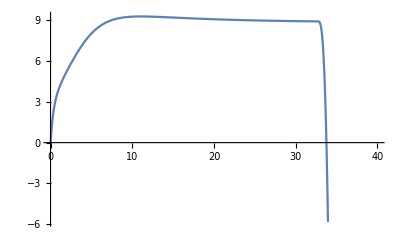

```mathematica
Plot[D1ir[t]/.NumSol,{t,0,40}]
```

This model is infeasible. The reason is because the prey population is guaranteed to either grow exponentially, or to decline to extinction, because the predator population cannot control the prey population: the maximum possible population size for the predators is given by the carrying capacity K. At that carrying capacity, the predator will either be able to drive the prey to exinction (if a_1 K_1+a_2 K_2>r_N) or the prey will grow exponentially. That is why I cannot find any equilibrium.

#### Model with density-dependent intermediate host growth

```mathematica
dNsdt=rN (Ns+Nir+Nim)(1-(Ns+Nir+Nim)/KN)-a1 Ns (D1s+D1ir+D1im)-a2 Ns (D2s+D2im)-β Ns (Pr+Pm);
dD1sdt=r1 (D1s+D1ir+D1im) (1-(D1s+D1ir+D1im)/K1)-a1 D1s (Nir+Nim);
dD2sdt=r2 (D2s+D2im) (1-(D2s+D2im)/K2)-a2 D2s Nim;

dNirdt=β Ns Pr-a1 Nir (D1s+D1ir+D1im)-a2 Nir(D2s+D2im)-μN Nir;
dNimdt=β Ns Pm-a1 Nim(D1s+D1ir+D1im)-a2 Nim(D2s+D2im)-μN Nim;

dD1irdt=a1 D1s Nir-μ1 D1ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;

dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
dPmdt=c λ1 D1im+c λ2 D2im-β Ns Pm-γ Pm;
```

```mathematica
J={{D[dNsdt,Ns], D[dNsdt,D1s], D[dNsdt,D2s],D[dNsdt,Nir],D[dNsdt,D1ir],D[dNsdt,Pr],D[dNsdt,Nim],D[dNsdt,D1im],D[dNsdt,D2im],D[dNsdt,Pm]},
{D[dD1sdt,Ns], D[dD1sdt,D1s], D[dD1sdt,D2s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr],D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD2sdt,Ns], D[dD2sdt,D1s], D[dD2sdt,D2s],D[dD2sdt,Nir],D[dD2sdt,D1ir],D[dD2sdt,Pr],D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dNirdt,Ns], D[dNirdt,D1s], D[dNirdt,D2s],D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr],D[dNirdt,Nim],D[dNirdt,D1im],D[dNirdt,D2im],D[dNirdt,Pm]},
{D[dD1irdt,Ns], D[dD1irdt,D1s], D[dD1irdt,D2s],D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr],D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dPrdt,Ns], D[dPrdt,D1s], D[dPrdt,D2s],D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr],D[dPrdt,Nim],D[dPrdt,D1im],D[dPrdt,D2im],D[dPrdt,Pm]},
{D[dNimdt,Ns], D[dNimdt,D1s], D[dNimdt,D2s],D[dNimdt,Nir],D[dNimdt,D1ir],D[dNimdt,Pr],D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,Ns], D[dD1imdt,D1s], D[dD1imdt,D2s],D[dD1imdt,Nir],D[dD1imdt,D1ir],D[dD1imdt,Pr],D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,Ns], D[dD2imdt,D1s], D[dD2imdt,D2s],D[dD2imdt,Nir],D[dD2imdt,D1ir],D[dD2imdt,Pr],D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,Ns], D[dPmdt,D1s], D[dPmdt,D2s],D[dPmdt,Nir],D[dPmdt,D1ir],D[dPmdt,Pr],D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}
};
MatrixForm[J/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 (D1ir+D1s)-a2 D2s-((Nir+Ns) rN)/KN+(1-(Nir+Ns)/KN) rN-Pr β | -a1 Ns | -a2 Ns | -((Nir+Ns) rN)/KN+(1-(Nir+Ns)/KN) rN | -a1 Ns | -Ns β | -((Nir+Ns) rN)/KN+(1-(Nir+Ns)/KN) rN | -a1 Ns | -a2 Ns | -Ns β
0 | -a1 Nir+(1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | 0
0 | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0 | 0 | 0 | -a2 D2s | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0
Pr β | -a1 Nir | -a2 Nir | -a1 (D1ir+D1s)-a2 D2s-μN | -a1 Nir | Ns β | 0 | -a1 Nir | -a2 Nir | 0
0 | a1 Nir | 0 | a1 D1s | -μ1 | 0 | 0 | 0 | 0 | 0
-Pr β | 0 | 0 | 0 | λ1 | -Ns β-γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a1 (D1ir+D1s)-a2 D2s-μN | 0 | 0 | Ns β
0 | 0 | 0 | 0 | 0 | 0 | a1 D1s | -μ1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a2 D2s | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | c λ1 | c λ2 | -Ns β-γ)

Because J is block triangular, the eigenvalues are given by the eigenvalues of the matrices on the diagonal. Whether invasion can happen or not depends entirely on the eigenvalues of the lower triangular matrix, given below. Note that -(-1)^(1/3)=-0.5-0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue:
(a^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1s+a2 D2s)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3))>1

```mathematica
MatrixForm[J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0}]
F={{0,0,0,Ns β},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1, c λ2,0}};
V={{a1 D1s+a1 D1ir+a2 D2s+μN,0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,Ns β+γ}};
(J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0})==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==(β Ns)/(β Ns+γ) ((a1 D1s)/(a1 D1s+a1 D1ir+a2 D2s+μN) (c λ1)/μ1+(a2 D2s)/(a1 D1s+a1 D1ir+a2 D2s+μN) (c λ2)/μ2)//Simplify
```

(-a1 (D1ir+D1s)-a2 D2s-μN | 0 | 0 | Ns β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -Ns β-γ)

True

{0,(c^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3) (a1 D1ir+a1 D1s+a2 D2s+μN)^(1/3)),-((-1)^(1/3) c^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3) (a1 D1ir+a1 D1s+a2 D2s+μN)^(1/3)),((-1)^(2/3) c^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3) (a1 D1ir+a1 D1s+a2 D2s+μN)^(1/3))}

True

The invasion fitness depends on OverHat[N_s], OverHat[D_(1s)], and OverHat[D_(2s)], the equilibria set by the resident parasite.

```mathematica
dNsdt=rN (Ns+Nir) (1-(Ns+Nir)/KN)-a1 Ns (D1s+D1ir)-a2 Ns K2-β Ns Pr;
dNirdt=β Ns Pr-a1 Nir (D1s+D1ir)-a2 Nir K2-μN Nir;
dD1sdt=r1 (D1s+D1ir) (1-(D1s+D1ir)/K1)-a1 D1s Nir;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

```mathematica
D1irEq=Simplify[Solve[dPrdt==0,D1ir][[1]]]
```

{D1ir→(Pr (Ns β+γ))/λ1}

```mathematica
D1sEq=Simplify[Solve[(dD1irdt/.D1irEq)==0,D1s][[1]]]
```

{D1s→(Pr (Ns β+γ) μ1)/(a1 Nir λ1)}

```mathematica
NsEq=Simplify[Solve[(dD1sdt/.D1irEq/.D1sEq)==0,Ns][[2]]]
```

{Ns→(a1 Nir r1 (-2 Pr γ+K1 λ1) μ1-Pr r1 γ μ1^2-a1^2 Nir^2 (Pr r1 γ+K1 λ1 (-r1+μ1)))/(Pr r1 β (a1 Nir+μ1)^2)}

```mathematica
PrEq=Simplify[Solve[(dNirdt/.D1irEq/.D1sEq/.NsEq)==0,Pr][[1]]]
```

{Pr→-(Nir (a1^3 K1 Nir^2 (r1-μ1)+r1 μ1^2 (a2 K2+μN)+a1 r1 μ1 (2 a2 K2 Nir+K1 (-λ1+μ1)+2 Nir μN)+a1^2 Nir (a2 K2 Nir r1-K1 (r1 λ1-2 r1 μ1-λ1 μ1+μ1^2)+Nir r1 μN)))/(r1 γ (a1 Nir+μ1)^2)}

You can plug these equilibria into the equation for the dynamcs of N_S, then try to solve for N_(I,r). However, the resulting polynomial to be solved is 7th degree, which means it will have no explicit solution. Thus, I cannot explicitly write down the equilibrium, and thus cannot explore how the invasion fitness (which depends on these equilibria) will be affected by changes in parameters.

```mathematica
Collect[Numerator[Together[(dNsdt/.D1irEq/.D1sEq/.NsEq/.PrEq)]],Nir]
```

-a1^3 K1^3 KN r1^3 β γ λ1 μ1^4-2 a1^2 a2 K1^2 K2 KN r1^3 β γ λ1 μ1^4-a1 a2^2 K1 K2^2 KN r1^3 β γ λ1 μ1^4+a1^2 K1^2 KN r1^3 rN β γ λ1 μ1^4+a1 a2 K1 K2 KN r1^3 rN β γ λ1 μ1^4+a1^3 K1^3 KN r1^3 β γ μ1^5+3 a1^2 a2 K1^2 K2 KN r1^3 β γ μ1^5+3 a1 a2^2 K1 K2^2 KN r1^3 β γ μ1^5+a2^3 K2^3 KN r1^3 β γ μ1^5-a1^2 K1^2 KN r1^3 rN β γ μ1^5-2 a1 a2 K1 K2 KN r1^3 rN β γ μ1^5-a2^2 K2^2 KN r1^3 rN β γ μ1^5-a1^2 K1^2 r1^3 rN γ^2 μ1^5-2 a1 a2 K1 K2 r1^3 rN γ^2 μ1^5-a2^2 K2^2 r1^3 rN γ^2 μ1^5-a1^2 K1^2 KN r1^3 β γ λ1 μ1^4 μN-a1 a2 K1 K2 KN r1^3 β γ λ1 μ1^4 μN+a1 K1 KN r1^3 rN β γ λ1 μ1^4 μN+2 a1^2 K1^2 KN r1^3 β γ μ1^5 μN+4 a1 a2 K1 K2 KN r1^3 β γ μ1^5 μN+2 a2^2 K2^2 KN r1^3 β γ μ1^5 μN-2 a1 K1 KN r1^3 rN β γ μ1^5 μN-2 a2 K2 KN r1^3 rN β γ μ1^5 μN-2 a1 K1 r1^3 rN γ^2 μ1^5 μN-2 a2 K2 r1^3 rN γ^2 μ1^5 μN+a1 K1 KN r1^3 β γ μ1^5 μN^2+a2 K2 KN r1^3 β γ μ1^5 μN^2-KN r1^3 rN β γ μ1^5 μN^2-r1^3 rN γ^2 μ1^5 μN^2+Nir^7 (-a1^7 K1^2 r1^3 rN β^2-2 a1^6 a2 K1 K2 r1^3 rN β^2-a1^5 a2^2 K2^2 r1^3 rN β^2+2 a1^7 K1^2 r1^2 rN β^2 μ1+2 a1^6 a2 K1 K2 r1^2 rN β^2 μ1-a1^7 K1^2 r1 rN β^2 μ1^2-2 a1^6 K1 r1^3 rN β^2 μN-2 a1^5 a2 K2 r1^3 rN β^2 μN+2 a1^6 K1 r1^2 rN β^2 μ1 μN-a1^5 r1^3 rN β^2 μN^2)+Nir^6 (-a1^8 K1^3 KN r1^3 β^2-3 a1^7 a2 K1^2 K2 KN r1^3 β^2-3 a1^6 a2^2 K1 K2^2 KN r1^3 β^2-a1^5 a2^3 K2^3 KN r1^3 β^2+a1^7 K1^2 KN r1^3 rN β^2+2 a1^6 a2 K1 K2 KN r1^3 rN β^2+a1^5 a2^2 K2^2 KN r1^3 rN β^2+2 a1^7 K1^2 r1^3 rN β γ+4 a1^6 a2 K1 K2 r1^3 rN β γ+2 a1^5 a2^2 K2^2 r1^3 rN β γ+2 a1^6 K1^2 r1^3 rN β^2 λ1+2 a1^5 a2 K1 K2 r1^3 rN β^2 λ1+3 a1^8 K1^3 KN r1^2 β^2 μ1+6 a1^7 a2 K1^2 K2 KN r1^2 β^2 μ1+3 a1^6 a2^2 K1 K2^2 KN r1^2 β^2 μ1-2 a1^7 K1^2 KN r1^2 rN β^2 μ1-2 a1^6 a2 K1 K2 KN r1^2 rN β^2 μ1-5 a1^6 K1^2 r1^3 rN β^2 μ1-10 a1^5 a2 K1 K2 r1^3 rN β^2 μ1-5 a1^4 a2^2 K2^2 r1^3 rN β^2 μ1-4 a1^7 K1^2 r1^2 rN β γ μ1-4 a1^6 a2 K1 K2 r1^2 rN β γ μ1-4 a1^6 K1^2 r1^2 rN β^2 λ1 μ1-2 a1^5 a2 K1 K2 r1^2 rN β^2 λ1 μ1-3 a1^8 K1^3 KN r1 β^2 μ1^2-3 a1^7 a2 K1^2 K2 KN r1 β^2 μ1^2+a1^7 K1^2 KN r1 rN β^2 μ1^2+8 a1^6 K1^2 r1^2 rN β^2 μ1^2+8 a1^5 a2 K1 K2 r1^2 rN β^2 μ1^2+2 a1^7 K1^2 r1 rN β γ μ1^2+2 a1^6 K1^2 r1 rN β^2 λ1 μ1^2+a1^8 K1^3 KN β^2 μ1^3-3 a1^6 K1^2 r1 rN β^2 μ1^3-3 a1^7 K1^2 KN r1^3 β^2 μN-6 a1^6 a2 K1 K2 KN r1^3 β^2 μN-3 a1^5 a2^2 K2^2 KN r1^3 β^2 μN+2 a1^6 K1 KN r1^3 rN β^2 μN+2 a1^5 a2 K2 KN r1^3 rN β^2 μN+4 a1^6 K1 r1^3 rN β γ μN+4 a1^5 a2 K2 r1^3 rN β γ μN+2 a1^5 K1 r1^3 rN β^2 λ1 μN+6 a1^7 K1^2 KN r1^2 β^2 μ1 μN+6 a1^6 a2 K1 K2 KN r1^2 β^2 μ1 μN-2 a1^6 K1 KN r1^2 rN β^2 μ1 μN-10 a1^5 K1 r1^3 rN β^2 μ1 μN-10 a1^4 a2 K2 r1^3 rN β^2 μ1 μN-4 a1^6 K1 r1^2 rN β γ μ1 μN-2 a1^5 K1 r1^2 rN β^2 λ1 μ1 μN-3 a1^7 K1^2 KN r1 β^2 μ1^2 μN+8 a1^5 K1 r1^2 rN β^2 μ1^2 μN-3 a1^6 K1 KN r1^3 β^2 μN^2-3 a1^5 a2 K2 KN r1^3 β^2 μN^2+a1^5 KN r1^3 rN β^2 μN^2+2 a1^5 r1^3 rN β γ μN^2+3 a1^6 K1 KN r1^2 β^2 μ1 μN^2-5 a1^4 r1^3 rN β^2 μ1 μN^2-a1^5 KN r1^3 β^2 μN^3)+Nir^5 (a1^8 K1^3 KN r1^3 β γ+3 a1^7 a2 K1^2 K2 KN r1^3 β γ+3 a1^6 a2^2 K1 K2^2 KN r1^3 β γ+a1^5 a2^3 K2^3 KN r1^3 β γ-a1^7 K1^2 KN r1^3 rN β γ-2 a1^6 a2 K1 K2 KN r1^3 rN β γ-a1^5 a2^2 K2^2 KN r1^3 rN β γ-a1^7 K1^2 r1^3 rN γ^2-2 a1^6 a2 K1 K2 r1^3 rN γ^2-a1^5 a2^2 K2^2 r1^3 rN γ^2+2 a1^7 K1^3 KN r1^3 β^2 λ1+4 a1^6 a2 K1^2 K2 KN r1^3 β^2 λ1+2 a1^5 a2^2 K1 K2^2 KN r1^3 β^2 λ1-2 a1^6 K1^2 KN r1^3 rN β^2 λ1-2 a1^5 a2 K1 K2 KN r1^3 rN β^2 λ1-2 a1^6 K1^2 r1^3 rN β γ λ1-2 a1^5 a2 K1 K2 r1^3 rN β γ λ1-a1^5 K1^2 r1^3 rN β^2 λ1^2-5 a1^7 K1^3 KN r1^3 β^2 μ1-15 a1^6 a2 K1^2 K2 KN r1^3 β^2 μ1-15 a1^5 a2^2 K1 K2^2 KN r1^3 β^2 μ1-5 a1^4 a2^3 K2^3 KN r1^3 β^2 μ1+5 a1^6 K1^2 KN r1^3 rN β^2 μ1+10 a1^5 a2 K1 K2 KN r1^3 rN β^2 μ1+5 a1^4 a2^2 K2^2 KN r1^3 rN β^2 μ1-3 a1^8 K1^3 KN r1^2 β γ μ1-6 a1^7 a2 K1^2 K2 KN r1^2 β γ μ1-3 a1^6 a2^2 K1 K2^2 KN r1^2 β γ μ1+2 a1^7 K1^2 KN r1^2 rN β γ μ1+2 a1^6 a2 K1 K2 KN r1^2 rN β γ μ1+10 a1^6 K1^2 r1^3 rN β γ μ1+20 a1^5 a2 K1 K2 r1^3 rN β γ μ1+10 a1^4 a2^2 K2^2 r1^3 rN β γ μ1+2 a1^7 K1^2 r1^2 rN γ^2 μ1+2 a1^6 a2 K1 K2 r1^2 rN γ^2 μ1-6 a1^7 K1^3 KN r1^2 β^2 λ1 μ1-8 a1^6 a2 K1^2 K2 KN r1^2 β^2 λ1 μ1-2 a1^5 a2^2 K1 K2^2 KN r1^2 β^2 λ1 μ1+4 a1^6 K1^2 KN r1^2 rN β^2 λ1 μ1+2 a1^5 a2 K1 K2 KN r1^2 rN β^2 λ1 μ1+8 a1^5 K1^2 r1^3 rN β^2 λ1 μ1+8 a1^4 a2 K1 K2 r1^3 rN β^2 λ1 μ1+4 a1^6 K1^2 r1^2 rN β γ λ1 μ1+2 a1^5 a2 K1 K2 r1^2 rN β γ λ1 μ1+2 a1^5 K1^2 r1^2 rN β^2 λ1^2 μ1+12 a1^7 K1^3 KN r1^2 β^2 μ1^2+24 a1^6 a2 K1^2 K2 KN r1^2 β^2 μ1^2+12 a1^5 a2^2 K1 K2^2 KN r1^2 β^2 μ1^2-8 a1^6 K1^2 KN r1^2 rN β^2 μ1^2-8 a1^5 a2 K1 K2 KN r1^2 rN β^2 μ1^2-10 a1^5 K1^2 r1^3 rN β^2 μ1^2-20 a1^4 a2 K1 K2 r1^3 rN β^2 μ1^2-10 a1^3 a2^2 K2^2 r1^3 rN β^2 μ1^2+3 a1^8 K1^3 KN r1 β γ μ1^2+3 a1^7 a2 K1^2 K2 KN r1 β γ μ1^2-a1^7 K1^2 KN r1 rN β γ μ1^2-16 a1^6 K1^2 r1^2 rN β γ μ1^2-16 a1^5 a2 K1 K2 r1^2 rN β γ μ1^2-a1^7 K1^2 r1 rN γ^2 μ1^2+6 a1^7 K1^3 KN r1 β^2 λ1 μ1^2+4 a1^6 a2 K1^2 K2 KN r1 β^2 λ1 μ1^2-2 a1^6 K1^2 KN r1 rN β^2 λ1 μ1^2-12 a1^5 K1^2 r1^2 rN β^2 λ1 μ1^2-6 a1^4 a2 K1 K2 r1^2 rN β^2 λ1 μ1^2-2 a1^6 K1^2 r1 rN β γ λ1 μ1^2-a1^5 K1^2 r1 rN β^2 λ1^2 μ1^2-9 a1^7 K1^3 KN r1 β^2 μ1^3-9 a1^6 a2 K1^2 K2 KN r1 β^2 μ1^3+3 a1^6 K1^2 KN r1 rN β^2 μ1^3+12 a1^5 K1^2 r1^2 rN β^2 μ1^3+12 a1^4 a2 K1 K2 r1^2 rN β^2 μ1^3-a1^8 K1^3 KN β γ μ1^3+6 a1^6 K1^2 r1 rN β γ μ1^3-2 a1^7 K1^3 KN β^2 λ1 μ1^3+4 a1^5 K1^2 r1 rN β^2 λ1 μ1^3+2 a1^7 K1^3 KN β^2 μ1^4-3 a1^5 K1^2 r1 rN β^2 μ1^4+2 a1^7 K1^2 KN r1^3 β γ μN+4 a1^6 a2 K1 K2 KN r1^3 β γ μN+2 a1^5 a2^2 K2^2 KN r1^3 β γ μN-2 a1^6 K1 KN r1^3 rN β γ μN-2 a1^5 a2 K2 KN r1^3 rN β γ μN-2 a1^6 K1 r1^3 rN γ^2 μN-2 a1^5 a2 K2 r1^3 rN γ^2 μN+4 a1^6 K1^2 KN r1^3 β^2 λ1 μN+4 a1^5 a2 K1 K2 KN r1^3 β^2 λ1 μN-2 a1^5 K1 KN r1^3 rN β^2 λ1 μN-2 a1^5 K1 r1^3 rN β γ λ1 μN-15 a1^6 K1^2 KN r1^3 β^2 μ1 μN-30 a1^5 a2 K1 K2 KN r1^3 β^2 μ1 μN-15 a1^4 a2^2 K2^2 KN r1^3 β^2 μ1 μN+10 a1^5 K1 KN r1^3 rN β^2 μ1 μN+10 a1^4 a2 K2 KN r1^3 rN β^2 μ1 μN-4 a1^7 K1^2 KN r1^2 β γ μ1 μN-4 a1^6 a2 K1 K2 KN r1^2 β γ μ1 μN+2 a1^6 K1 KN r1^2 rN β γ μ1 μN+20 a1^5 K1 r1^3 rN β γ μ1 μN+20 a1^4 a2 K2 r1^3 rN β γ μ1 μN+2 a1^6 K1 r1^2 rN γ^2 μ1 μN-8 a1^6 K1^2 KN r1^2 β^2 λ1 μ1 μN-4 a1^5 a2 K1 K2 KN r1^2 β^2 λ1 μ1 μN+2 a1^5 K1 KN r1^2 rN β^2 λ1 μ1 μN+8 a1^4 K1 r1^3 rN β^2 λ1 μ1 μN+2 a1^5 K1 r1^2 rN β γ λ1 μ1 μN+24 a1^6 K1^2 KN r1^2 β^2 μ1^2 μN+24 a1^5 a2 K1 K2 KN r1^2 β^2 μ1^2 μN-8 a1^5 K1 KN r1^2 rN β^2 μ1^2 μN-20 a1^4 K1 r1^3 rN β^2 μ1^2 μN-20 a1^3 a2 K2 r1^3 rN β^2 μ1^2 μN+2 a1^7 K1^2 KN r1 β γ μ1^2 μN-16 a1^5 K1 r1^2 rN β γ μ1^2 μN+4 a1^6 K1^2 KN r1 β^2 λ1 μ1^2 μN-6 a1^4 K1 r1^2 rN β^2 λ1 μ1^2 μN-9 a1^6 K1^2 KN r1 β^2 μ1^3 μN+12 a1^4 K1 r1^2 rN β^2 μ1^3 μN+a1^6 K1 KN r1^3 β γ μN^2+a1^5 a2 K2 KN r1^3 β γ μN^2-a1^5 KN r1^3 rN β γ μN^2-a1^5 r1^3 rN γ^2 μN^2+2 a1^5 K1 KN r1^3 β^2 λ1 μN^2-15 a1^5 K1 KN r1^3 β^2 μ1 μN^2-15 a1^4 a2 K2 KN r1^3 β^2 μ1 μN^2+5 a1^4 KN r1^3 rN β^2 μ1 μN^2-a1^6 K1 KN r1^2 β γ μ1 μN^2+10 a1^4 r1^3 rN β γ μ1 μN^2-2 a1^5 K1 KN r1^2 β^2 λ1 μ1 μN^2+12 a1^5 K1 KN r1^2 β^2 μ1^2 μN^2-10 a1^3 r1^3 rN β^2 μ1^2 μN^2-5 a1^4 KN r1^3 β^2 μ1 μN^3)+Nir^4 (-a1^7 K1^3 KN r1^3 β γ λ1-2 a1^6 a2 K1^2 K2 KN r1^3 β γ λ1-a1^5 a2^2 K1 K2^2 KN r1^3 β γ λ1+a1^6 K1^2 KN r1^3 rN β γ λ1+a1^5 a2 K1 K2 KN r1^3 rN β γ λ1-a1^6 K1^3 KN r1^3 β^2 λ1^2-a1^5 a2 K1^2 K2 KN r1^3 β^2 λ1^2+a1^5 K1^2 KN r1^3 rN β^2 λ1^2+5 a1^7 K1^3 KN r1^3 β γ μ1+15 a1^6 a2 K1^2 K2 KN r1^3 β γ μ1+15 a1^5 a2^2 K1 K2^2 KN r1^3 β γ μ1+5 a1^4 a2^3 K2^3 KN r1^3 β γ μ1-5 a1^6 K1^2 KN r1^3 rN β γ μ1-10 a1^5 a2 K1 K2 KN r1^3 rN β γ μ1-5 a1^4 a2^2 K2^2 KN r1^3 rN β γ μ1-5 a1^6 K1^2 r1^3 rN γ^2 μ1-10 a1^5 a2 K1 K2 r1^3 rN γ^2 μ1-5 a1^4 a2^2 K2^2 r1^3 rN γ^2 μ1+8 a1^6 K1^3 KN r1^3 β^2 λ1 μ1+16 a1^5 a2 K1^2 K2 KN r1^3 β^2 λ1 μ1+8 a1^4 a2^2 K1 K2^2 KN r1^3 β^2 λ1 μ1-8 a1^5 K1^2 KN r1^3 rN β^2 λ1 μ1-8 a1^4 a2 K1 K2 KN r1^3 rN β^2 λ1 μ1+3 a1^7 K1^3 KN r1^2 β γ λ1 μ1+4 a1^6 a2 K1^2 K2 KN r1^2 β γ λ1 μ1+a1^5 a2^2 K1 K2^2 KN r1^2 β γ λ1 μ1-2 a1^6 K1^2 KN r1^2 rN β γ λ1 μ1-a1^5 a2 K1 K2 KN r1^2 rN β γ λ1 μ1-8 a1^5 K1^2 r1^3 rN β γ λ1 μ1-8 a1^4 a2 K1 K2 r1^3 rN β γ λ1 μ1+3 a1^6 K1^3 KN r1^2 β^2 λ1^2 μ1+2 a1^5 a2 K1^2 K2 KN r1^2 β^2 λ1^2 μ1-2 a1^5 K1^2 KN r1^2 rN β^2 λ1^2 μ1-3 a1^4 K1^2 r1^3 rN β^2 λ1^2 μ1-10 a1^6 K1^3 KN r1^3 β^2 μ1^2-30 a1^5 a2 K1^2 K2 KN r1^3 β^2 μ1^2-30 a1^4 a2^2 K1 K2^2 KN r1^3 β^2 μ1^2-10 a1^3 a2^3 K2^3 KN r1^3 β^2 μ1^2+10 a1^5 K1^2 KN r1^3 rN β^2 μ1^2+20 a1^4 a2 K1 K2 KN r1^3 rN β^2 μ1^2+10 a1^3 a2^2 K2^2 KN r1^3 rN β^2 μ1^2-12 a1^7 K1^3 KN r1^2 β γ μ1^2-24 a1^6 a2 K1^2 K2 KN r1^2 β γ μ1^2-12 a1^5 a2^2 K1 K2^2 KN r1^2 β γ μ1^2+8 a1^6 K1^2 KN r1^2 rN β γ μ1^2+8 a1^5 a2 K1 K2 KN r1^2 rN β γ μ1^2+20 a1^5 K1^2 r1^3 rN β γ μ1^2+40 a1^4 a2 K1 K2 r1^3 rN β γ μ1^2+20 a1^3 a2^2 K2^2 r1^3 rN β γ μ1^2+8 a1^6 K1^2 r1^2 rN γ^2 μ1^2+8 a1^5 a2 K1 K2 r1^2 rN γ^2 μ1^2-18 a1^6 K1^3 KN r1^2 β^2 λ1 μ1^2-24 a1^5 a2 K1^2 K2 KN r1^2 β^2 λ1 μ1^2-6 a1^4 a2^2 K1 K2^2 KN r1^2 β^2 λ1 μ1^2+12 a1^5 K1^2 KN r1^2 rN β^2 λ1 μ1^2+6 a1^4 a2 K1 K2 KN r1^2 rN β^2 λ1 μ1^2+12 a1^4 K1^2 r1^3 rN β^2 λ1 μ1^2+12 a1^3 a2 K1 K2 r1^3 rN β^2 λ1 μ1^2-3 a1^7 K1^3 KN r1 β γ λ1 μ1^2-2 a1^6 a2 K1^2 K2 KN r1 β γ λ1 μ1^2+a1^6 K1^2 KN r1 rN β γ λ1 μ1^2+12 a1^5 K1^2 r1^2 rN β γ λ1 μ1^2+6 a1^4 a2 K1 K2 r1^2 rN β γ λ1 μ1^2-3 a1^6 K1^3 KN r1 β^2 λ1^2 μ1^2-a1^5 a2 K1^2 K2 KN r1 β^2 λ1^2 μ1^2+a1^5 K1^2 KN r1 rN β^2 λ1^2 μ1^2+4 a1^4 K1^2 r1^2 rN β^2 λ1^2 μ1^2+18 a1^6 K1^3 KN r1^2 β^2 μ1^3+36 a1^5 a2 K1^2 K2 KN r1^2 β^2 μ1^3+18 a1^4 a2^2 K1 K2^2 KN r1^2 β^2 μ1^3-12 a1^5 K1^2 KN r1^2 rN β^2 μ1^3-12 a1^4 a2 K1 K2 KN r1^2 rN β^2 μ1^3-10 a1^4 K1^2 r1^3 rN β^2 μ1^3-20 a1^3 a2 K1 K2 r1^3 rN β^2 μ1^3-10 a1^2 a2^2 K2^2 r1^3 rN β^2 μ1^3+9 a1^7 K1^3 KN r1 β γ μ1^3+9 a1^6 a2 K1^2 K2 KN r1 β γ μ1^3-3 a1^6 K1^2 KN r1 rN β γ μ1^3-24 a1^5 K1^2 r1^2 rN β γ μ1^3-24 a1^4 a2 K1 K2 r1^2 rN β γ μ1^3-3 a1^6 K1^2 r1 rN γ^2 μ1^3+12 a1^6 K1^3 KN r1 β^2 λ1 μ1^3+8 a1^5 a2 K1^2 K2 KN r1 β^2 λ1 μ1^3-4 a1^5 K1^2 KN r1 rN β^2 λ1 μ1^3-12 a1^4 K1^2 r1^2 rN β^2 λ1 μ1^3-6 a1^3 a2 K1 K2 r1^2 rN β^2 λ1 μ1^3+a1^7 K1^3 KN β γ λ1 μ1^3-4 a1^5 K1^2 r1 rN β γ λ1 μ1^3+a1^6 K1^3 KN β^2 λ1^2 μ1^3-a1^4 K1^2 r1 rN β^2 λ1^2 μ1^3-9 a1^6 K1^3 KN r1 β^2 μ1^4-9 a1^5 a2 K1^2 K2 KN r1 β^2 μ1^4+3 a1^5 K1^2 KN r1 rN β^2 μ1^4+8 a1^4 K1^2 r1^2 rN β^2 μ1^4+8 a1^3 a2 K1 K2 r1^2 rN β^2 μ1^4-2 a1^7 K1^3 KN β γ μ1^4+6 a1^5 K1^2 r1 rN β γ μ1^4-2 a1^6 K1^3 KN β^2 λ1 μ1^4+2 a1^4 K1^2 r1 rN β^2 λ1 μ1^4+a1^6 K1^3 KN β^2 μ1^5-a1^4 K1^2 r1 rN β^2 μ1^5-a1^6 K1^2 KN r1^3 β γ λ1 μN-a1^5 a2 K1 K2 KN r1^3 β γ λ1 μN+a1^5 K1 KN r1^3 rN β γ λ1 μN-a1^5 K1^2 KN r1^3 β^2 λ1^2 μN+10 a1^6 K1^2 KN r1^3 β γ μ1 μN+20 a1^5 a2 K1 K2 KN r1^3 β γ μ1 μN+10 a1^4 a2^2 K2^2 KN r1^3 β γ μ1 μN-10 a1^5 K1 KN r1^3 rN β γ μ1 μN-10 a1^4 a2 K2 KN r1^3 rN β γ μ1 μN-10 a1^5 K1 r1^3 rN γ^2 μ1 μN-10 a1^4 a2 K2 r1^3 rN γ^2 μ1 μN+16 a1^5 K1^2 KN r1^3 β^2 λ1 μ1 μN+16 a1^4 a2 K1 K2 KN r1^3 β^2 λ1 μ1 μN-8 a1^4 K1 KN r1^3 rN β^2 λ1 μ1 μN+2 a1^6 K1^2 KN r1^2 β γ λ1 μ1 μN+a1^5 a2 K1 K2 KN r1^2 β γ λ1 μ1 μN-a1^5 K1 KN r1^2 rN β γ λ1 μ1 μN-8 a1^4 K1 r1^3 rN β γ λ1 μ1 μN+2 a1^5 K1^2 KN r1^2 β^2 λ1^2 μ1 μN-30 a1^5 K1^2 KN r1^3 β^2 μ1^2 μN-60 a1^4 a2 K1 K2 KN r1^3 β^2 μ1^2 μN-30 a1^3 a2^2 K2^2 KN r1^3 β^2 μ1^2 μN+20 a1^4 K1 KN r1^3 rN β^2 μ1^2 μN+20 a1^3 a2 K2 KN r1^3 rN β^2 μ1^2 μN-16 a1^6 K1^2 KN r1^2 β γ μ1^2 μN-16 a1^5 a2 K1 K2 KN r1^2 β γ μ1^2 μN+8 a1^5 K1 KN r1^2 rN β γ μ1^2 μN+40 a1^4 K1 r1^3 rN β γ μ1^2 μN+40 a1^3 a2 K2 r1^3 rN β γ μ1^2 μN+8 a1^5 K1 r1^2 rN γ^2 μ1^2 μN-24 a1^5 K1^2 KN r1^2 β^2 λ1 μ1^2 μN-12 a1^4 a2 K1 K2 KN r1^2 β^2 λ1 μ1^2 μN+6 a1^4 K1 KN r1^2 rN β^2 λ1 μ1^2 μN+12 a1^3 K1 r1^3 rN β^2 λ1 μ1^2 μN-a1^6 K1^2 KN r1 β γ λ1 μ1^2 μN+6 a1^4 K1 r1^2 rN β γ λ1 μ1^2 μN-a1^5 K1^2 KN r1 β^2 λ1^2 μ1^2 μN+36 a1^5 K1^2 KN r1^2 β^2 μ1^3 μN+36 a1^4 a2 K1 K2 KN r1^2 β^2 μ1^3 μN-12 a1^4 K1 KN r1^2 rN β^2 μ1^3 μN-20 a1^3 K1 r1^3 rN β^2 μ1^3 μN-20 a1^2 a2 K2 r1^3 rN β^2 μ1^3 μN+6 a1^6 K1^2 KN r1 β γ μ1^3 μN-24 a1^4 K1 r1^2 rN β γ μ1^3 μN+8 a1^5 K1^2 KN r1 β^2 λ1 μ1^3 μN-6 a1^3 K1 r1^2 rN β^2 λ1 μ1^3 μN-9 a1^5 K1^2 KN r1 β^2 μ1^4 μN+8 a1^3 K1 r1^2 rN β^2 μ1^4 μN+5 a1^5 K1 KN r1^3 β γ μ1 μN^2+5 a1^4 a2 K2 KN r1^3 β γ μ1 μN^2-5 a1^4 KN r1^3 rN β γ μ1 μN^2-5 a1^4 r1^3 rN γ^2 μ1 μN^2+8 a1^4 K1 KN r1^3 β^2 λ1 μ1 μN^2-30 a1^4 K1 KN r1^3 β^2 μ1^2 μN^2-30 a1^3 a2 K2 KN r1^3 β^2 μ1^2 μN^2+10 a1^3 KN r1^3 rN β^2 μ1^2 μN^2-4 a1^5 K1 KN r1^2 β γ μ1^2 μN^2+20 a1^3 r1^3 rN β γ μ1^2 μN^2-6 a1^4 K1 KN r1^2 β^2 λ1 μ1^2 μN^2+18 a1^4 K1 KN r1^2 β^2 μ1^3 μN^2-10 a1^2 r1^3 rN β^2 μ1^3 μN^2-10 a1^3 KN r1^3 β^2 μ1^2 μN^3)+Nir^3 (-4 a1^6 K1^3 KN r1^3 β γ λ1 μ1-8 a1^5 a2 K1^2 K2 KN r1^3 β γ λ1 μ1-4 a1^4 a2^2 K1 K2^2 KN r1^3 β γ λ1 μ1+4 a1^5 K1^2 KN r1^3 rN β γ λ1 μ1+4 a1^4 a2 K1 K2 KN r1^3 rN β γ λ1 μ1-3 a1^5 K1^3 KN r1^3 β^2 λ1^2 μ1-3 a1^4 a2 K1^2 K2 KN r1^3 β^2 λ1^2 μ1+3 a1^4 K1^2 KN r1^3 rN β^2 λ1^2 μ1+10 a1^6 K1^3 KN r1^3 β γ μ1^2+30 a1^5 a2 K1^2 K2 KN r1^3 β γ μ1^2+30 a1^4 a2^2 K1 K2^2 KN r1^3 β γ μ1^2+10 a1^3 a2^3 K2^3 KN r1^3 β γ μ1^2-10 a1^5 K1^2 KN r1^3 rN β γ μ1^2-20 a1^4 a2 K1 K2 KN r1^3 rN β γ μ1^2-10 a1^3 a2^2 K2^2 KN r1^3 rN β γ μ1^2-10 a1^5 K1^2 r1^3 rN γ^2 μ1^2-20 a1^4 a2 K1 K2 r1^3 rN γ^2 μ1^2-10 a1^3 a2^2 K2^2 r1^3 rN γ^2 μ1^2+12 a1^5 K1^3 KN r1^3 β^2 λ1 μ1^2+24 a1^4 a2 K1^2 K2 KN r1^3 β^2 λ1 μ1^2+12 a1^3 a2^2 K1 K2^2 KN r1^3 β^2 λ1 μ1^2-12 a1^4 K1^2 KN r1^3 rN β^2 λ1 μ1^2-12 a1^3 a2 K1 K2 KN r1^3 rN β^2 λ1 μ1^2+9 a1^6 K1^3 KN r1^2 β γ λ1 μ1^2+12 a1^5 a2 K1^2 K2 KN r1^2 β γ λ1 μ1^2+3 a1^4 a2^2 K1 K2^2 KN r1^2 β γ λ1 μ1^2-6 a1^5 K1^2 KN r1^2 rN β γ λ1 μ1^2-3 a1^4 a2 K1 K2 KN r1^2 rN β γ λ1 μ1^2-12 a1^4 K1^2 r1^3 rN β γ λ1 μ1^2-12 a1^3 a2 K1 K2 r1^3 rN β γ λ1 μ1^2+6 a1^5 K1^3 KN r1^2 β^2 λ1^2 μ1^2+4 a1^4 a2 K1^2 K2 KN r1^2 β^2 λ1^2 μ1^2-4 a1^4 K1^2 KN r1^2 rN β^2 λ1^2 μ1^2-3 a1^3 K1^2 r1^3 rN β^2 λ1^2 μ1^2-10 a1^5 K1^3 KN r1^3 β^2 μ1^3-30 a1^4 a2 K1^2 K2 KN r1^3 β^2 μ1^3-30 a1^3 a2^2 K1 K2^2 KN r1^3 β^2 μ1^3-10 a1^2 a2^3 K2^3 KN r1^3 β^2 μ1^3+10 a1^4 K1^2 KN r1^3 rN β^2 μ1^3+20 a1^3 a2 K1 K2 KN r1^3 rN β^2 μ1^3+10 a1^2 a2^2 K2^2 KN r1^3 rN β^2 μ1^3-18 a1^6 K1^3 KN r1^2 β γ μ1^3-36 a1^5 a2 K1^2 K2 KN r1^2 β γ μ1^3-18 a1^4 a2^2 K1 K2^2 KN r1^2 β γ μ1^3+12 a1^5 K1^2 KN r1^2 rN β γ μ1^3+12 a1^4 a2 K1 K2 KN r1^2 rN β γ μ1^3+20 a1^4 K1^2 r1^3 rN β γ μ1^3+40 a1^3 a2 K1 K2 r1^3 rN β γ μ1^3+20 a1^2 a2^2 K2^2 r1^3 rN β γ μ1^3+12 a1^5 K1^2 r1^2 rN γ^2 μ1^3+12 a1^4 a2 K1 K2 r1^2 rN γ^2 μ1^3-18 a1^5 K1^3 KN r1^2 β^2 λ1 μ1^3-24 a1^4 a2 K1^2 K2 KN r1^2 β^2 λ1 μ1^3-6 a1^3 a2^2 K1 K2^2 KN r1^2 β^2 λ1 μ1^3+12 a1^4 K1^2 KN r1^2 rN β^2 λ1 μ1^3+6 a1^3 a2 K1 K2 KN r1^2 rN β^2 λ1 μ1^3+8 a1^3 K1^2 r1^3 rN β^2 λ1 μ1^3+8 a1^2 a2 K1 K2 r1^3 rN β^2 λ1 μ1^3-6 a1^6 K1^3 KN r1 β γ λ1 μ1^3-4 a1^5 a2 K1^2 K2 KN r1 β γ λ1 μ1^3+2 a1^5 K1^2 KN r1 rN β γ λ1 μ1^3+12 a1^4 K1^2 r1^2 rN β γ λ1 μ1^3+6 a1^3 a2 K1 K2 r1^2 rN β γ λ1 μ1^3-3 a1^5 K1^3 KN r1 β^2 λ1^2 μ1^3-a1^4 a2 K1^2 K2 KN r1 β^2 λ1^2 μ1^3+a1^4 K1^2 KN r1 rN β^2 λ1^2 μ1^3+2 a1^3 K1^2 r1^2 rN β^2 λ1^2 μ1^3+12 a1^5 K1^3 KN r1^2 β^2 μ1^4+24 a1^4 a2 K1^2 K2 KN r1^2 β^2 μ1^4+12 a1^3 a2^2 K1 K2^2 KN r1^2 β^2 μ1^4-8 a1^4 K1^2 KN r1^2 rN β^2 μ1^4-8 a1^3 a2 K1 K2 KN r1^2 rN β^2 μ1^4-5 a1^3 K1^2 r1^3 rN β^2 μ1^4-10 a1^2 a2 K1 K2 r1^3 rN β^2 μ1^4-5 a1 a2^2 K2^2 r1^3 rN β^2 μ1^4+9 a1^6 K1^3 KN r1 β γ μ1^4+9 a1^5 a2 K1^2 K2 KN r1 β γ μ1^4-3 a1^5 K1^2 KN r1 rN β γ μ1^4-16 a1^4 K1^2 r1^2 rN β γ μ1^4-16 a1^3 a2 K1 K2 r1^2 rN β γ μ1^4-3 a1^5 K1^2 r1 rN γ^2 μ1^4+6 a1^5 K1^3 KN r1 β^2 λ1 μ1^4+4 a1^4 a2 K1^2 K2 KN r1 β^2 λ1 μ1^4-2 a1^4 K1^2 KN r1 rN β^2 λ1 μ1^4-4 a1^3 K1^2 r1^2 rN β^2 λ1 μ1^4-2 a1^2 a2 K1 K2 r1^2 rN β^2 λ1 μ1^4+a1^6 K1^3 KN β γ λ1 μ1^4-2 a1^4 K1^2 r1 rN β γ λ1 μ1^4-3 a1^5 K1^3 KN r1 β^2 μ1^5-3 a1^4 a2 K1^2 K2 KN r1 β^2 μ1^5+a1^4 K1^2 KN r1 rN β^2 μ1^5+2 a1^3 K1^2 r1^2 rN β^2 μ1^5+2 a1^2 a2 K1 K2 r1^2 rN β^2 μ1^5-a1^6 K1^3 KN β γ μ1^5+2 a1^4 K1^2 r1 rN β γ μ1^5-4 a1^5 K1^2 KN r1^3 β γ λ1 μ1 μN-4 a1^4 a2 K1 K2 KN r1^3 β γ λ1 μ1 μN+4 a1^4 K1 KN r1^3 rN β γ λ1 μ1 μN-3 a1^4 K1^2 KN r1^3 β^2 λ1^2 μ1 μN+20 a1^5 K1^2 KN r1^3 β γ μ1^2 μN+40 a1^4 a2 K1 K2 KN r1^3 β γ μ1^2 μN+20 a1^3 a2^2 K2^2 KN r1^3 β γ μ1^2 μN-20 a1^4 K1 KN r1^3 rN β γ μ1^2 μN-20 a1^3 a2 K2 KN r1^3 rN β γ μ1^2 μN-20 a1^4 K1 r1^3 rN γ^2 μ1^2 μN-20 a1^3 a2 K2 r1^3 rN γ^2 μ1^2 μN+24 a1^4 K1^2 KN r1^3 β^2 λ1 μ1^2 μN+24 a1^3 a2 K1 K2 KN r1^3 β^2 λ1 μ1^2 μN-12 a1^3 K1 KN r1^3 rN β^2 λ1 μ1^2 μN+6 a1^5 K1^2 KN r1^2 β γ λ1 μ1^2 μN+3 a1^4 a2 K1 K2 KN r1^2 β γ λ1 μ1^2 μN-3 a1^4 K1 KN r1^2 rN β γ λ1 μ1^2 μN-12 a1^3 K1 r1^3 rN β γ λ1 μ1^2 μN+4 a1^4 K1^2 KN r1^2 β^2 λ1^2 μ1^2 μN-30 a1^4 K1^2 KN r1^3 β^2 μ1^3 μN-60 a1^3 a2 K1 K2 KN r1^3 β^2 μ1^3 μN-30 a1^2 a2^2 K2^2 KN r1^3 β^2 μ1^3 μN+20 a1^3 K1 KN r1^3 rN β^2 μ1^3 μN+20 a1^2 a2 K2 KN r1^3 rN β^2 μ1^3 μN-24 a1^5 K1^2 KN r1^2 β γ μ1^3 μN-24 a1^4 a2 K1 K2 KN r1^2 β γ μ1^3 μN+12 a1^4 K1 KN r1^2 rN β γ μ1^3 μN+40 a1^3 K1 r1^3 rN β γ μ1^3 μN+40 a1^2 a2 K2 r1^3 rN β γ μ1^3 μN+12 a1^4 K1 r1^2 rN γ^2 μ1^3 μN-24 a1^4 K1^2 KN r1^2 β^2 λ1 μ1^3 μN-12 a1^3 a2 K1 K2 KN r1^2 β^2 λ1 μ1^3 μN+6 a1^3 K1 KN r1^2 rN β^2 λ1 μ1^3 μN+8 a1^2 K1 r1^3 rN β^2 λ1 μ1^3 μN-2 a1^5 K1^2 KN r1 β γ λ1 μ1^3 μN+6 a1^3 K1 r1^2 rN β γ λ1 μ1^3 μN-a1^4 K1^2 KN r1 β^2 λ1^2 μ1^3 μN+24 a1^4 K1^2 KN r1^2 β^2 μ1^4 μN+24 a1^3 a2 K1 K2 KN r1^2 β^2 μ1^4 μN-8 a1^3 K1 KN r1^2 rN β^2 μ1^4 μN-10 a1^2 K1 r1^3 rN β^2 μ1^4 μN-10 a1 a2 K2 r1^3 rN β^2 μ1^4 μN+6 a1^5 K1^2 KN r1 β γ μ1^4 μN-16 a1^3 K1 r1^2 rN β γ μ1^4 μN+4 a1^4 K1^2 KN r1 β^2 λ1 μ1^4 μN-2 a1^2 K1 r1^2 rN β^2 λ1 μ1^4 μN-3 a1^4 K1^2 KN r1 β^2 μ1^5 μN+2 a1^2 K1 r1^2 rN β^2 μ1^5 μN+10 a1^4 K1 KN r1^3 β γ μ1^2 μN^2+10 a1^3 a2 K2 KN r1^3 β γ μ1^2 μN^2-10 a1^3 KN r1^3 rN β γ μ1^2 μN^2-10 a1^3 r1^3 rN γ^2 μ1^2 μN^2+12 a1^3 K1 KN r1^3 β^2 λ1 μ1^2 μN^2-30 a1^3 K1 KN r1^3 β^2 μ1^3 μN^2-30 a1^2 a2 K2 KN r1^3 β^2 μ1^3 μN^2+10 a1^2 KN r1^3 rN β^2 μ1^3 μN^2-6 a1^4 K1 KN r1^2 β γ μ1^3 μN^2+20 a1^2 r1^3 rN β γ μ1^3 μN^2-6 a1^3 K1 KN r1^2 β^2 λ1 μ1^3 μN^2+12 a1^3 K1 KN r1^2 β^2 μ1^4 μN^2-5 a1 r1^3 rN β^2 μ1^4 μN^2-10 a1^2 KN r1^3 β^2 μ1^3 μN^3)+Nir^2 (-6 a1^5 K1^3 KN r1^3 β γ λ1 μ1^2-12 a1^4 a2 K1^2 K2 KN r1^3 β γ λ1 μ1^2-6 a1^3 a2^2 K1 K2^2 KN r1^3 β γ λ1 μ1^2+6 a1^4 K1^2 KN r1^3 rN β γ λ1 μ1^2+6 a1^3 a2 K1 K2 KN r1^3 rN β γ λ1 μ1^2-3 a1^4 K1^3 KN r1^3 β^2 λ1^2 μ1^2-3 a1^3 a2 K1^2 K2 KN r1^3 β^2 λ1^2 μ1^2+3 a1^3 K1^2 KN r1^3 rN β^2 λ1^2 μ1^2+10 a1^5 K1^3 KN r1^3 β γ μ1^3+30 a1^4 a2 K1^2 K2 KN r1^3 β γ μ1^3+30 a1^3 a2^2 K1 K2^2 KN r1^3 β γ μ1^3+10 a1^2 a2^3 K2^3 KN r1^3 β γ μ1^3-10 a1^4 K1^2 KN r1^3 rN β γ μ1^3-20 a1^3 a2 K1 K2 KN r1^3 rN β γ μ1^3-10 a1^2 a2^2 K2^2 KN r1^3 rN β γ μ1^3-10 a1^4 K1^2 r1^3 rN γ^2 μ1^3-20 a1^3 a2 K1 K2 r1^3 rN γ^2 μ1^3-10 a1^2 a2^2 K2^2 r1^3 rN γ^2 μ1^3+8 a1^4 K1^3 KN r1^3 β^2 λ1 μ1^3+16 a1^3 a2 K1^2 K2 KN r1^3 β^2 λ1 μ1^3+8 a1^2 a2^2 K1 K2^2 KN r1^3 β^2 λ1 μ1^3-8 a1^3 K1^2 KN r1^3 rN β^2 λ1 μ1^3-8 a1^2 a2 K1 K2 KN r1^3 rN β^2 λ1 μ1^3+9 a1^5 K1^3 KN r1^2 β γ λ1 μ1^3+12 a1^4 a2 K1^2 K2 KN r1^2 β γ λ1 μ1^3+3 a1^3 a2^2 K1 K2^2 KN r1^2 β γ λ1 μ1^3-6 a1^4 K1^2 KN r1^2 rN β γ λ1 μ1^3-3 a1^3 a2 K1 K2 KN r1^2 rN β γ λ1 μ1^3-8 a1^3 K1^2 r1^3 rN β γ λ1 μ1^3-8 a1^2 a2 K1 K2 r1^3 rN β γ λ1 μ1^3+3 a1^4 K1^3 KN r1^2 β^2 λ1^2 μ1^3+2 a1^3 a2 K1^2 K2 KN r1^2 β^2 λ1^2 μ1^3-2 a1^3 K1^2 KN r1^2 rN β^2 λ1^2 μ1^3-a1^2 K1^2 r1^3 rN β^2 λ1^2 μ1^3-5 a1^4 K1^3 KN r1^3 β^2 μ1^4-15 a1^3 a2 K1^2 K2 KN r1^3 β^2 μ1^4-15 a1^2 a2^2 K1 K2^2 KN r1^3 β^2 μ1^4-5 a1 a2^3 K2^3 KN r1^3 β^2 μ1^4+5 a1^3 K1^2 KN r1^3 rN β^2 μ1^4+10 a1^2 a2 K1 K2 KN r1^3 rN β^2 μ1^4+5 a1 a2^2 K2^2 KN r1^3 rN β^2 μ1^4-12 a1^5 K1^3 KN r1^2 β γ μ1^4-24 a1^4 a2 K1^2 K2 KN r1^2 β γ μ1^4-12 a1^3 a2^2 K1 K2^2 KN r1^2 β γ μ1^4+8 a1^4 K1^2 KN r1^2 rN β γ μ1^4+8 a1^3 a2 K1 K2 KN r1^2 rN β γ μ1^4+10 a1^3 K1^2 r1^3 rN β γ μ1^4+20 a1^2 a2 K1 K2 r1^3 rN β γ μ1^4+10 a1 a2^2 K2^2 r1^3 rN β γ μ1^4+8 a1^4 K1^2 r1^2 rN γ^2 μ1^4+8 a1^3 a2 K1 K2 r1^2 rN γ^2 μ1^4-6 a1^4 K1^3 KN r1^2 β^2 λ1 μ1^4-8 a1^3 a2 K1^2 K2 KN r1^2 β^2 λ1 μ1^4-2 a1^2 a2^2 K1 K2^2 KN r1^2 β^2 λ1 μ1^4+4 a1^3 K1^2 KN r1^2 rN β^2 λ1 μ1^4+2 a1^2 a2 K1 K2 KN r1^2 rN β^2 λ1 μ1^4+2 a1^2 K1^2 r1^3 rN β^2 λ1 μ1^4+2 a1 a2 K1 K2 r1^3 rN β^2 λ1 μ1^4-3 a1^5 K1^3 KN r1 β γ λ1 μ1^4-2 a1^4 a2 K1^2 K2 KN r1 β γ λ1 μ1^4+a1^4 K1^2 KN r1 rN β γ λ1 μ1^4+4 a1^3 K1^2 r1^2 rN β γ λ1 μ1^4+2 a1^2 a2 K1 K2 r1^2 rN β γ λ1 μ1^4+3 a1^4 K1^3 KN r1^2 β^2 μ1^5+6 a1^3 a2 K1^2 K2 KN r1^2 β^2 μ1^5+3 a1^2 a2^2 K1 K2^2 KN r1^2 β^2 μ1^5-2 a1^3 K1^2 KN r1^2 rN β^2 μ1^5-2 a1^2 a2 K1 K2 KN r1^2 rN β^2 μ1^5-a1^2 K1^2 r1^3 rN β^2 μ1^5-2 a1 a2 K1 K2 r1^3 rN β^2 μ1^5-a2^2 K2^2 r1^3 rN β^2 μ1^5+3 a1^5 K1^3 KN r1 β γ μ1^5+3 a1^4 a2 K1^2 K2 KN r1 β γ μ1^5-a1^4 K1^2 KN r1 rN β γ μ1^5-4 a1^3 K1^2 r1^2 rN β γ μ1^5-4 a1^2 a2 K1 K2 r1^2 rN β γ μ1^5-a1^4 K1^2 r1 rN γ^2 μ1^5-6 a1^4 K1^2 KN r1^3 β γ λ1 μ1^2 μN-6 a1^3 a2 K1 K2 KN r1^3 β γ λ1 μ1^2 μN+6 a1^3 K1 KN r1^3 rN β γ λ1 μ1^2 μN-3 a1^3 K1^2 KN r1^3 β^2 λ1^2 μ1^2 μN+20 a1^4 K1^2 KN r1^3 β γ μ1^3 μN+40 a1^3 a2 K1 K2 KN r1^3 β γ μ1^3 μN+20 a1^2 a2^2 K2^2 KN r1^3 β γ μ1^3 μN-20 a1^3 K1 KN r1^3 rN β γ μ1^3 μN-20 a1^2 a2 K2 KN r1^3 rN β γ μ1^3 μN-20 a1^3 K1 r1^3 rN γ^2 μ1^3 μN-20 a1^2 a2 K2 r1^3 rN γ^2 μ1^3 μN+16 a1^3 K1^2 KN r1^3 β^2 λ1 μ1^3 μN+16 a1^2 a2 K1 K2 KN r1^3 β^2 λ1 μ1^3 μN-8 a1^2 K1 KN r1^3 rN β^2 λ1 μ1^3 μN+6 a1^4 K1^2 KN r1^2 β γ λ1 μ1^3 μN+3 a1^3 a2 K1 K2 KN r1^2 β γ λ1 μ1^3 μN-3 a1^3 K1 KN r1^2 rN β γ λ1 μ1^3 μN-8 a1^2 K1 r1^3 rN β γ λ1 μ1^3 μN+2 a1^3 K1^2 KN r1^2 β^2 λ1^2 μ1^3 μN-15 a1^3 K1^2 KN r1^3 β^2 μ1^4 μN-30 a1^2 a2 K1 K2 KN r1^3 β^2 μ1^4 μN-15 a1 a2^2 K2^2 KN r1^3 β^2 μ1^4 μN+10 a1^2 K1 KN r1^3 rN β^2 μ1^4 μN+10 a1 a2 K2 KN r1^3 rN β^2 μ1^4 μN-16 a1^4 K1^2 KN r1^2 β γ μ1^4 μN-16 a1^3 a2 K1 K2 KN r1^2 β γ μ1^4 μN+8 a1^3 K1 KN r1^2 rN β γ μ1^4 μN+20 a1^2 K1 r1^3 rN β γ μ1^4 μN+20 a1 a2 K2 r1^3 rN β γ μ1^4 μN+8 a1^3 K1 r1^2 rN γ^2 μ1^4 μN-8 a1^3 K1^2 KN r1^2 β^2 λ1 μ1^4 μN-4 a1^2 a2 K1 K2 KN r1^2 β^2 λ1 μ1^4 μN+2 a1^2 K1 KN r1^2 rN β^2 λ1 μ1^4 μN+2 a1 K1 r1^3 rN β^2 λ1 μ1^4 μN-a1^4 K1^2 KN r1 β γ λ1 μ1^4 μN+2 a1^2 K1 r1^2 rN β γ λ1 μ1^4 μN+6 a1^3 K1^2 KN r1^2 β^2 μ1^5 μN+6 a1^2 a2 K1 K2 KN r1^2 β^2 μ1^5 μN-2 a1^2 K1 KN r1^2 rN β^2 μ1^5 μN-2 a1 K1 r1^3 rN β^2 μ1^5 μN-2 a2 K2 r1^3 rN β^2 μ1^5 μN+2 a1^4 K1^2 KN r1 β γ μ1^5 μN-4 a1^2 K1 r1^2 rN β γ μ1^5 μN+10 a1^3 K1 KN r1^3 β γ μ1^3 μN^2+10 a1^2 a2 K2 KN r1^3 β γ μ1^3 μN^2-10 a1^2 KN r1^3 rN β γ μ1^3 μN^2-10 a1^2 r1^3 rN γ^2 μ1^3 μN^2+8 a1^2 K1 KN r1^3 β^2 λ1 μ1^3 μN^2-15 a1^2 K1 KN r1^3 β^2 μ1^4 μN^2-15 a1 a2 K2 KN r1^3 β^2 μ1^4 μN^2+5 a1 KN r1^3 rN β^2 μ1^4 μN^2-4 a1^3 K1 KN r1^2 β γ μ1^4 μN^2+10 a1 r1^3 rN β γ μ1^4 μN^2-2 a1^2 K1 KN r1^2 β^2 λ1 μ1^4 μN^2+3 a1^2 K1 KN r1^2 β^2 μ1^5 μN^2-r1^3 rN β^2 μ1^5 μN^2-5 a1 KN r1^3 β^2 μ1^4 μN^3)+Nir (-4 a1^4 K1^3 KN r1^3 β γ λ1 μ1^3-8 a1^3 a2 K1^2 K2 KN r1^3 β γ λ1 μ1^3-4 a1^2 a2^2 K1 K2^2 KN r1^3 β γ λ1 μ1^3+4 a1^3 K1^2 KN r1^3 rN β γ λ1 μ1^3+4 a1^2 a2 K1 K2 KN r1^3 rN β γ λ1 μ1^3-a1^3 K1^3 KN r1^3 β^2 λ1^2 μ1^3-a1^2 a2 K1^2 K2 KN r1^3 β^2 λ1^2 μ1^3+a1^2 K1^2 KN r1^3 rN β^2 λ1^2 μ1^3+5 a1^4 K1^3 KN r1^3 β γ μ1^4+15 a1^3 a2 K1^2 K2 KN r1^3 β γ μ1^4+15 a1^2 a2^2 K1 K2^2 KN r1^3 β γ μ1^4+5 a1 a2^3 K2^3 KN r1^3 β γ μ1^4-5 a1^3 K1^2 KN r1^3 rN β γ μ1^4-10 a1^2 a2 K1 K2 KN r1^3 rN β γ μ1^4-5 a1 a2^2 K2^2 KN r1^3 rN β γ μ1^4-5 a1^3 K1^2 r1^3 rN γ^2 μ1^4-10 a1^2 a2 K1 K2 r1^3 rN γ^2 μ1^4-5 a1 a2^2 K2^2 r1^3 rN γ^2 μ1^4+2 a1^3 K1^3 KN r1^3 β^2 λ1 μ1^4+4 a1^2 a2 K1^2 K2 KN r1^3 β^2 λ1 μ1^4+2 a1 a2^2 K1 K2^2 KN r1^3 β^2 λ1 μ1^4-2 a1^2 K1^2 KN r1^3 rN β^2 λ1 μ1^4-2 a1 a2 K1 K2 KN r1^3 rN β^2 λ1 μ1^4+3 a1^4 K1^3 KN r1^2 β γ λ1 μ1^4+4 a1^3 a2 K1^2 K2 KN r1^2 β γ λ1 μ1^4+a1^2 a2^2 K1 K2^2 KN r1^2 β γ λ1 μ1^4-2 a1^3 K1^2 KN r1^2 rN β γ λ1 μ1^4-a1^2 a2 K1 K2 KN r1^2 rN β γ λ1 μ1^4-2 a1^2 K1^2 r1^3 rN β γ λ1 μ1^4-2 a1 a2 K1 K2 r1^3 rN β γ λ1 μ1^4-a1^3 K1^3 KN r1^3 β^2 μ1^5-3 a1^2 a2 K1^2 K2 KN r1^3 β^2 μ1^5-3 a1 a2^2 K1 K2^2 KN r1^3 β^2 μ1^5-a2^3 K2^3 KN r1^3 β^2 μ1^5+a1^2 K1^2 KN r1^3 rN β^2 μ1^5+2 a1 a2 K1 K2 KN r1^3 rN β^2 μ1^5+a2^2 K2^2 KN r1^3 rN β^2 μ1^5-3 a1^4 K1^3 KN r1^2 β γ μ1^5-6 a1^3 a2 K1^2 K2 KN r1^2 β γ μ1^5-3 a1^2 a2^2 K1 K2^2 KN r1^2 β γ μ1^5+2 a1^3 K1^2 KN r1^2 rN β γ μ1^5+2 a1^2 a2 K1 K2 KN r1^2 rN β γ μ1^5+2 a1^2 K1^2 r1^3 rN β γ μ1^5+4 a1 a2 K1 K2 r1^3 rN β γ μ1^5+2 a2^2 K2^2 r1^3 rN β γ μ1^5+2 a1^3 K1^2 r1^2 rN γ^2 μ1^5+2 a1^2 a2 K1 K2 r1^2 rN γ^2 μ1^5-4 a1^3 K1^2 KN r1^3 β γ λ1 μ1^3 μN-4 a1^2 a2 K1 K2 KN r1^3 β γ λ1 μ1^3 μN+4 a1^2 K1 KN r1^3 rN β γ λ1 μ1^3 μN-a1^2 K1^2 KN r1^3 β^2 λ1^2 μ1^3 μN+10 a1^3 K1^2 KN r1^3 β γ μ1^4 μN+20 a1^2 a2 K1 K2 KN r1^3 β γ μ1^4 μN+10 a1 a2^2 K2^2 KN r1^3 β γ μ1^4 μN-10 a1^2 K1 KN r1^3 rN β γ μ1^4 μN-10 a1 a2 K2 KN r1^3 rN β γ μ1^4 μN-10 a1^2 K1 r1^3 rN γ^2 μ1^4 μN-10 a1 a2 K2 r1^3 rN γ^2 μ1^4 μN+4 a1^2 K1^2 KN r1^3 β^2 λ1 μ1^4 μN+4 a1 a2 K1 K2 KN r1^3 β^2 λ1 μ1^4 μN-2 a1 K1 KN r1^3 rN β^2 λ1 μ1^4 μN+2 a1^3 K1^2 KN r1^2 β γ λ1 μ1^4 μN+a1^2 a2 K1 K2 KN r1^2 β γ λ1 μ1^4 μN-a1^2 K1 KN r1^2 rN β γ λ1 μ1^4 μN-2 a1 K1 r1^3 rN β γ λ1 μ1^4 μN-3 a1^2 K1^2 KN r1^3 β^2 μ1^5 μN-6 a1 a2 K1 K2 KN r1^3 β^2 μ1^5 μN-3 a2^2 K2^2 KN r1^3 β^2 μ1^5 μN+2 a1 K1 KN r1^3 rN β^2 μ1^5 μN+2 a2 K2 KN r1^3 rN β^2 μ1^5 μN-4 a1^3 K1^2 KN r1^2 β γ μ1^5 μN-4 a1^2 a2 K1 K2 KN r1^2 β γ μ1^5 μN+2 a1^2 K1 KN r1^2 rN β γ μ1^5 μN+4 a1 K1 r1^3 rN β γ μ1^5 μN+4 a2 K2 r1^3 rN β γ μ1^5 μN+2 a1^2 K1 r1^2 rN γ^2 μ1^5 μN+5 a1^2 K1 KN r1^3 β γ μ1^4 μN^2+5 a1 a2 K2 KN r1^3 β γ μ1^4 μN^2-5 a1 KN r1^3 rN β γ μ1^4 μN^2-5 a1 r1^3 rN γ^2 μ1^4 μN^2+2 a1 K1 KN r1^3 β^2 λ1 μ1^4 μN^2-3 a1 K1 KN r1^3 β^2 μ1^5 μN^2-3 a2 K2 KN r1^3 β^2 μ1^5 μN^2+KN r1^3 rN β^2 μ1^5 μN^2-a1^2 K1 KN r1^2 β γ μ1^5 μN^2+2 r1^3 rN β γ μ1^5 μN^2-KN r1^3 β^2 μ1^5 μN^3)

#### Model with constant intermediate host population size

Looking at the previous model analyses, the invasion fitness itself is pretty independendent of what is happening with the intermediate host, save for the expression N_S/(N_S+γ), which determines the probability that a parasite in the environment infects an intermediate host before it is lost from the environment. If I assume a constant intermediate host population size, then I can keep track of the fraction of the population that is susceptible versus infected. Let N_S and N_I be the fraction of intermediate hosts that are susceptible and infected, and let N_T be the total population size of the intermediate hosts. In order for there to be a persistence equilibrium, I must introduce demography, even though the population size will still remain constant.

```mathematica
dNsdt=a1 (D1s+D1ir+D1im+D2s+D2im)-β Ns Pr-a1 (D1s+D1ir+D1im+D2s+D2im) Ns;
dNirdt=β Ns Pr-a1 (D1s+D1ir+D1im+D2s+D2im) Nir;
dNimdt=β Ns Pm-a1 (D1s+D1ir+D1im+D2s+D2im) Nim;
dD1sdt=r1 (D1s+D1ir+D1im) (1-(D1s+D1ir+D1im)/K1)-a1 D1s (Nir+Nim) NT;
dD2sdt=r2 (D2s+D2im) (1-(D2s+D2im)/K2)-a2 D2s Nim NT;
dD1irdt=a1 D1s Nir NT-μ1 D1ir;
dD1imdt=a1 D1s Nim NT-μ1 D1im;
dD2imdt=a2 D2s Nim NT-μ2 D2im;
dPrdt=λ1 D1ir-β Ns NT Pr-γ Pr;
dPmdt=c λ1 D1im+c λ2 D2im-β Ns NT Pm-γ Pm;
```

```mathematica
J={{D[dNsdt,Ns], D[dNsdt,D1s], D[dNsdt,D2s],D[dNsdt,Nir],D[dNsdt,D1ir],D[dNsdt,Pr],D[dNsdt,Nim],D[dNsdt,D1im],D[dNsdt,D2im],D[dNsdt,Pm]},
{D[dD1sdt,Ns], D[dD1sdt,D1s], D[dD1sdt,D2s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr],D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD2sdt,Ns], D[dD2sdt,D1s], D[dD2sdt,D2s],D[dD2sdt,Nir],D[dD2sdt,D1ir],D[dD2sdt,Pr],D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dNirdt,Ns], D[dNirdt,D1s], D[dNirdt,D2s],D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr],D[dNirdt,Nim],D[dNirdt,D1im],D[dNirdt,D2im],D[dNirdt,Pm]},
{D[dD1irdt,Ns], D[dD1irdt,D1s], D[dD1irdt,D2s],D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr],D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dPrdt,Ns], D[dPrdt,D1s], D[dPrdt,D2s],D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr],D[dPrdt,Nim],D[dPrdt,D1im],D[dPrdt,D2im],D[dPrdt,Pm]},
{D[dNimdt,Ns], D[dNimdt,D1s], D[dNimdt,D2s],D[dNimdt,Nir],D[dNimdt,D1ir],D[dNimdt,Pr],D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,Ns], D[dD1imdt,D1s], D[dD1imdt,D2s],D[dD1imdt,Nir],D[dD1imdt,D1ir],D[dD1imdt,Pr],D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,Ns], D[dD2imdt,D1s], D[dD2imdt,D2s],D[dD2imdt,Nir],D[dD2imdt,D1ir],D[dD2imdt,Pr],D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,Ns], D[dPmdt,D1s], D[dPmdt,D2s],D[dPmdt,Nir],D[dPmdt,D1ir],D[dPmdt,Pr],D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}
};
MatrixForm[J/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 (D1ir+D1s+D2s)-Pr β | a1-a1 Ns | a1-a1 Ns | 0 | a1-a1 Ns | -Ns β | 0 | a1-a1 Ns | a1-a1 Ns | 0
0 | -a1 Nir NT+(1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s NT | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s NT | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | 0
0 | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0 | 0 | 0 | -a2 D2s NT | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0
Pr β | -a1 Nir | -a1 Nir | -a1 (D1ir+D1s+D2s) | -a1 Nir | Ns β | 0 | -a1 Nir | -a1 Nir | 0
0 | a1 Nir NT | 0 | a1 D1s NT | -μ1 | 0 | 0 | 0 | 0 | 0
-NT Pr β | 0 | 0 | 0 | λ1 | -Ns NT β-γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a1 (D1ir+D1s+D2s) | 0 | 0 | Ns β
0 | 0 | 0 | 0 | 0 | 0 | a1 D1s NT | -μ1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a2 D2s NT | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | c λ1 | c λ2 | -Ns NT β-γ)

Because J is block triangular, the eigenvalues are given by the eigenvalues of the matrices on the diagonal. Whether invasion can happen or not depends entirely on the eigenvalues of the lower triangular matrix, given below. Note that -(-1)^(1/3)=-0.5-0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue:
(a^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1s+a2 D2s)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3))>1

```mathematica
MatrixForm[J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0}]
F={{0,0,0,Ns β},{a1 D1s NT,0,0,0},{a2 D2s NT,0,0,0},{0,c λ1, c λ2,0}};
V={{a1 (D1ir+D1s+D2s),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,Ns NT β+γ}};
(J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0})==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==(β Ns NT)/(β Ns NT+γ) ((a1 D1s)/(a1 (D1s+D1ir+D2s)) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir+D2s)) (c λ2)/μ2)//Simplify
```

(-a1 (D1ir+D1s+D2s) | 0 | 0 | Ns β
a1 D1s NT | -μ1 | 0 | 0
a2 D2s NT | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -Ns NT β-γ)

True

{0,(c^(1/3) Ns^(1/3) NT^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/(a1^(1/3) (D1ir+D1s+D2s)^(1/3) (Ns NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) c^(1/3) Ns^(1/3) NT^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/(a1^(1/3) (D1ir+D1s+D2s)^(1/3) (Ns NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) c^(1/3) Ns^(1/3) NT^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/(a1^(1/3) (D1ir+D1s+D2s)^(1/3) (Ns NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3))}

True

```mathematica
dNsdt=a1 (D1s+D1ir)-β Ns Pr-a1 (D1s+D1ir) Ns;
dNirdt=β Ns Pr-a1 (D1s+D1ir) Nir ;
dD1sdt=r1 (D1s+D1ir) (1-(D1s+D1ir)/K1)-a1 D1s Nir NT;
dD1irdt=a1 D1s Nir NT-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns NT Pr-γ Pr;
```

```mathematica
PrEq=Simplify[Solve[dNsdt==0,Pr][[1]]]
```

{Pr→-(a1 (D1ir+D1s) (-1+Ns))/(Ns β)}

```mathematica
NsEq=Solve[(dNirdt/.PrEq)==0,Ns][[1]]
```

{Ns→1-Nir}

```mathematica
PrEq=PrEq/.NsEq
```

{Pr→(a1 (D1ir+D1s) Nir)/((1-Nir) β)}

```mathematica
NirEq=Simplify[Solve[dD1sdt==0,Nir]][[1]]
```

{Nir→-((D1ir+D1s) (D1ir+D1s-K1) r1)/(a1 D1s K1 NT)}

```mathematica
D1sEq=Simplify[Solve[(dD1irdt/.NirEq)==0,D1s][[2]]]
```

{D1s→(-2 D1ir r1+K1 r1+√K1 √(r1 (K1 r1-4 D1ir μ1)))/(2 r1)}

This can be solved, although it seems unlikely that there will be much insight that can be gained from it!

```mathematica
Simplify[Solve[Numerator[Simplify[dPrdt/.PrEq/.NsEq/.NirEq/.D1sEq]]==0,D1ir]]
```

{{D1ir→0},{D1ir→1/(2 r1 β^2 λ1^2 (a1 NT+μ1)^2)K1 (a1^2 (-γ^2 μ1^3-NT β γ μ1 (r1 λ1+2 μ1 (-λ1+μ1))+NT^2 β^2 (r1 λ1 (2 λ1-μ1)-μ1 (2 λ1^2-2 λ1 μ1+μ1^2)))-β μ1^2 (r1 λ1+μ1 (-λ1+μ1)) (β (-λ1+μ1)+√(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1))))-a1 μ1 (γ μ1 (r1 β λ1+μ1 (2 β μ1+√(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1)))))+NT β (r1 λ1 (-3 β λ1+2 β μ1+√(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1))))+μ1 (2 β (λ1-μ1)^2+(-2 λ1+μ1) √(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1)))))))},{D1ir→1/(2 r1 β^2 λ1^2 (a1 NT+μ1)^2)K1 (a1^2 (-γ^2 μ1^3-NT β γ μ1 (r1 λ1+2 μ1 (-λ1+μ1))+NT^2 β^2 (r1 λ1 (2 λ1-μ1)-μ1 (2 λ1^2-2 λ1 μ1+μ1^2)))+β μ1^2 (r1 λ1+μ1 (-λ1+μ1)) (β (λ1-μ1)+√(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1))))+a1 μ1 (γ μ1 (-r1 β λ1+μ1 (-2 β μ1+√(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1)))))+NT β (r1 λ1 (3 β λ1-2 β μ1+√(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1))))+μ1 (-2 β (λ1-μ1)^2+(-2 λ1+μ1) √(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1)))))))}}

#### When can a generalist trophically transmitted parasite invade a system with two specialists, each infecting the same intermediate host?

Looking at the previous model analyses, the invasion fitness itself is pretty independendent of what is happening with the intermediate host, save for the expression N_S/(N_S+γ), which determines the probability that a parasite in the environment infects an intermediate host before it is lost from the environment. If I assume a constant intermediate host population size, then I can keep track of the fraction of the population that is susceptible versus infected. Let N_S and N_I be the fraction of intermediate hosts that are susceptible and infected, and let N_T be the total population size of the intermediate hosts. In order for there to be a persistence equilibrium, I must introduce demography, even though the population size will still remain constant.

Let K be the intermediate host population size (which is assumed to be constant); let N_(1,r) be the fraction of the intermediate host population infected by the first specialist parasite; let N_(2,r) be the fraction of the intermediate host population infected by the second specialist parasite. Let D_(1,s) be the number of susceptibles for the first definitive host and let D_(2,s) be the number of susceptibles of the second definitive host. Let I_(1,r) and I_(2,r) be the numbers of definitive hosts infected by the specialist parasites, and let I_(1,m) and I_(2,m) be the numbers of definitive hosts infected by the generalist parasite. Let P_(1,r) and P_(2,r) be the numbers of the two specialist parasites in the environment and let P_(12,m) be the number of generalist parasites in the environment.

```mathematica
dN1rdt=β 

dNirdt=β Ns Pr-a1 (D1s+D1ir+D1im+D2s+D2im) Nir;
dNimdt=β Ns Pm-a1 (D1s+D1ir+D1im+D2s+D2im) Nim;
dD1sdt=r1 (D1s+D1ir+D1im) (1-(D1s+D1ir+D1im)/K1)-a1 D1s (Nir+Nim) NT;
dD2sdt=r2 (D2s+D2im) (1-(D2s+D2im)/K2)-a2 D2s Nim NT;
dD1irdt=a1 D1s Nir NT-μ1 D1ir;
dD1imdt=a1 D1s Nim NT-μ1 D1im;
dD2imdt=a2 D2s Nim NT-μ2 D2im;
dPrdt=λ1 D1ir-β Ns NT Pr-γ Pr;
dPmdt=c λ1 D1im+c λ2 D2im-β Ns NT Pm-γ Pm;
```

```mathematica
J={{D[dNsdt,Ns], D[dNsdt,D1s], D[dNsdt,D2s],D[dNsdt,Nir],D[dNsdt,D1ir],D[dNsdt,Pr],D[dNsdt,Nim],D[dNsdt,D1im],D[dNsdt,D2im],D[dNsdt,Pm]},
{D[dD1sdt,Ns], D[dD1sdt,D1s], D[dD1sdt,D2s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr],D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD2sdt,Ns], D[dD2sdt,D1s], D[dD2sdt,D2s],D[dD2sdt,Nir],D[dD2sdt,D1ir],D[dD2sdt,Pr],D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dNirdt,Ns], D[dNirdt,D1s], D[dNirdt,D2s],D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr],D[dNirdt,Nim],D[dNirdt,D1im],D[dNirdt,D2im],D[dNirdt,Pm]},
{D[dD1irdt,Ns], D[dD1irdt,D1s], D[dD1irdt,D2s],D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr],D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dPrdt,Ns], D[dPrdt,D1s], D[dPrdt,D2s],D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr],D[dPrdt,Nim],D[dPrdt,D1im],D[dPrdt,D2im],D[dPrdt,Pm]},
{D[dNimdt,Ns], D[dNimdt,D1s], D[dNimdt,D2s],D[dNimdt,Nir],D[dNimdt,D1ir],D[dNimdt,Pr],D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,Ns], D[dD1imdt,D1s], D[dD1imdt,D2s],D[dD1imdt,Nir],D[dD1imdt,D1ir],D[dD1imdt,Pr],D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,Ns], D[dD2imdt,D1s], D[dD2imdt,D2s],D[dD2imdt,Nir],D[dD2imdt,D1ir],D[dD2imdt,Pr],D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,Ns], D[dPmdt,D1s], D[dPmdt,D2s],D[dPmdt,Nir],D[dPmdt,D1ir],D[dPmdt,Pr],D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}
};
MatrixForm[J/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 (D1ir+D1s+D2s)-Pr β | a1-a1 Ns | a1-a1 Ns | 0 | a1-a1 Ns | -Ns β | 0 | a1-a1 Ns | a1-a1 Ns | 0
0 | -a1 Nir NT+(1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s NT | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s NT | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | 0
0 | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0 | 0 | 0 | -a2 D2s NT | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0
Pr β | -a1 Nir | -a1 Nir | -a1 (D1ir+D1s+D2s) | -a1 Nir | Ns β | 0 | -a1 Nir | -a1 Nir | 0
0 | a1 Nir NT | 0 | a1 D1s NT | -μ1 | 0 | 0 | 0 | 0 | 0
-NT Pr β | 0 | 0 | 0 | λ1 | -Ns NT β-γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a1 (D1ir+D1s+D2s) | 0 | 0 | Ns β
0 | 0 | 0 | 0 | 0 | 0 | a1 D1s NT | -μ1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a2 D2s NT | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | c λ1 | c λ2 | -Ns NT β-γ)

Because J is block triangular, the eigenvalues are given by the eigenvalues of the matrices on the diagonal. Whether invasion can happen or not depends entirely on the eigenvalues of the lower triangular matrix, given below. Note that -(-1)^(1/3)=-0.5-0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue:
(a^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1s+a2 D2s)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3))>1

```mathematica
MatrixForm[J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0}]
F={{0,0,0,Ns β},{a1 D1s NT,0,0,0},{a2 D2s NT,0,0,0},{0,c λ1, c λ2,0}};
V={{a1 (D1ir+D1s+D2s),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,Ns NT β+γ}};
(J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0})==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==(β Ns NT)/(β Ns NT+γ) ((a1 D1s)/(a1 (D1s+D1ir+D2s)) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir+D2s)) (c λ2)/μ2)//Simplify
```

(-a1 (D1ir+D1s+D2s) | 0 | 0 | Ns β
a1 D1s NT | -μ1 | 0 | 0
a2 D2s NT | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -Ns NT β-γ)

True

{0,(c^(1/3) Ns^(1/3) NT^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/(a1^(1/3) (D1ir+D1s+D2s)^(1/3) (Ns NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) c^(1/3) Ns^(1/3) NT^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/(a1^(1/3) (D1ir+D1s+D2s)^(1/3) (Ns NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) c^(1/3) Ns^(1/3) NT^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/(a1^(1/3) (D1ir+D1s+D2s)^(1/3) (Ns NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3))}

True

```mathematica
dNsdt=a1 (D1s+D1ir)-β Ns Pr-a1 (D1s+D1ir) Ns;
dNirdt=β Ns Pr-a1 (D1s+D1ir) Nir ;
dD1sdt=r1 (D1s+D1ir) (1-(D1s+D1ir)/K1)-a1 D1s Nir NT;
dD1irdt=a1 D1s Nir NT-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns NT Pr-γ Pr;
```

```mathematica
PrEq=Simplify[Solve[dNsdt==0,Pr][[1]]]
```

{Pr→-(a1 (D1ir+D1s) (-1+Ns))/(Ns β)}

```mathematica
NsEq=Solve[(dNirdt/.PrEq)==0,Ns][[1]]
```

{Ns→1-Nir}

```mathematica
PrEq=PrEq/.NsEq
```

{Pr→(a1 (D1ir+D1s) Nir)/((1-Nir) β)}

```mathematica
NirEq=Simplify[Solve[dD1sdt==0,Nir]][[1]]
```

{Nir→-((D1ir+D1s) (D1ir+D1s-K1) r1)/(a1 D1s K1 NT)}

```mathematica
D1sEq=Simplify[Solve[(dD1irdt/.NirEq)==0,D1s][[2]]]
```

{D1s→(-2 D1ir r1+K1 r1+√K1 √(r1 (K1 r1-4 D1ir μ1)))/(2 r1)}

This can be solved, although it seems unlikely that there will be much insight that can be gained from it!

```mathematica
Simplify[Solve[Numerator[Simplify[dPrdt/.PrEq/.NsEq/.NirEq/.D1sEq]]==0,D1ir]]
```

{{D1ir→0},{D1ir→1/(2 r1 β^2 λ1^2 (a1 NT+μ1)^2)K1 (a1^2 (-γ^2 μ1^3-NT β γ μ1 (r1 λ1+2 μ1 (-λ1+μ1))+NT^2 β^2 (r1 λ1 (2 λ1-μ1)-μ1 (2 λ1^2-2 λ1 μ1+μ1^2)))-β μ1^2 (r1 λ1+μ1 (-λ1+μ1)) (β (-λ1+μ1)+√(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1))))-a1 μ1 (γ μ1 (r1 β λ1+μ1 (2 β μ1+√(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1)))))+NT β (r1 λ1 (-3 β λ1+2 β μ1+√(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1))))+μ1 (2 β (λ1-μ1)^2+(-2 λ1+μ1) √(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1)))))))},{D1ir→1/(2 r1 β^2 λ1^2 (a1 NT+μ1)^2)K1 (a1^2 (-γ^2 μ1^3-NT β γ μ1 (r1 λ1+2 μ1 (-λ1+μ1))+NT^2 β^2 (r1 λ1 (2 λ1-μ1)-μ1 (2 λ1^2-2 λ1 μ1+μ1^2)))+β μ1^2 (r1 λ1+μ1 (-λ1+μ1)) (β (λ1-μ1)+√(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1))))+a1 μ1 (γ μ1 (-r1 β λ1+μ1 (-2 β μ1+√(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1)))))+NT β (r1 λ1 (3 β λ1-2 β μ1+√(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1))))+μ1 (-2 β (λ1-μ1)^2+(-2 λ1+μ1) √(a1^2 (NT β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (NT β (-λ1+μ1)+γ (λ1+μ1)))))))}}

#### Model with constant pre

#### True predator-prey model

```mathematica
dNsdt=rN (Ns+Nir) (1-(Ns+Nir)/KN)-β Ns Pr-a1 (D1s+D1ir) Ns;
dNirdt=β Ns Pr-a1 (D1s+D1ir) Nir ;
dD1sdt=b a1 (D1s+D1ir) (Ns+Nir)-a1 D1s Nir-μ1 D1s;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

Before going any further, notice that the dynamics of the total predator population depend only on the total predator population and the total prey population. Thus we can solve directly for the total prey population at equilibrium.

```mathematica
Simplify[dD1sdt+dD1irdt]
Solve[((dD1sdt+dD1irdt)/.Ns->Ntot-Nir)==0,Ntot]
```

(D1ir+D1s) (a1 b (Nir+Ns)-μ1)

{{Ntot→μ1/(a1 b)}}

From this, you can see that the equilibrium total prey population will be N_S+N_(I,r)=μ_1/(b a_1). At the same time, the dynamics of the total prey population depend only on the total predator and prey populations, so we can also find for the total predator population at equililbrium.

```mathematica
Simplify[dNsdt+dNirdt]
Solve[(dNsdt+dNirdt/.D1s->Dtot-D1ir/.Ns->μ1/(b a1)-Nir)==0,Dtot]
```

-((Nir+Ns) (a1 (D1ir+D1s) KN+(-KN+Nir+Ns) rN))/KN

{{Dtot→(rN (a1 b KN-μ1))/(a1^2 b KN)}}

This greatly simplifies the dynamics, as we can drop two equations from the systemN_S completely (it is determined entirely by the equilibrium for N_(I,r)) and we can replace N_S+N_(I,r) with μ_1/(b a_1) everywhere else.

Notice that this really simplifies the dynamics of D_(1,S) in particular, from (dD_(1,S))/dt=b a_1(D_(1,S)+D_(1I,r))(N_S+N_(I,r))-a_1 D_(1,S)N_(I,r)-μ_1 D_(1,S)=μ_1(D_(1,S)+D_(1I,r))-a_1 D_(1,S)N_(I,r)-μ_1 D_(1,S)=μ_1 D_(1I,r)-a_1 D_(1,S)N_(I,r)

```mathematica
dNirdt=dNirdt/.{Ns->μ1/(a1 b)-Nir}/.{D1s->(rN (a1 b KN-μ1))/(a1^2 b KN)-D1ir}
dD1irdt=dD1irdt/.{D1s->(rN (a1 b KN-μ1))/(a1^2 b KN)-D1ir}
dPrdt=λ1 D1ir-β Ns Pr-γ Pr/.{Ns->μ1/(a1 b)-Nir}
```

-(Nir rN (a1 b KN-μ1))/(a1 b KN)+Pr β (-Nir+μ1/(a1 b))

a1 Nir (-D1ir+(rN (a1 b KN-μ1))/(a1^2 b KN))-D1ir μ1

-Pr γ+D1ir λ1-Pr β (-Nir+μ1/(a1 b))

```mathematica
Simplify[Solve[{dNirdt==0,dD1irdt==0,dPrdt==0},{Nir,D1ir,Pr}]]
```

{{Nir→0,D1ir→0,Pr→0},{Nir→(a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))/(2 a1^2 b β),D1ir→1/(4 a1^4 b^2 (1+b) KN β^2 λ1 μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (a1^2 b γ+a1 b β λ1+a1 β μ1+a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))),Pr→1/(4 a1^4 b^2 (1+b) KN β^2 γ μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (a1^2 b γ+a1 b β λ1-a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))},{Nir→(a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))/(2 a1^2 b β),D1ir→1/(4 a1^4 b^2 (1+b) KN β^2 λ1 μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1+a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))),Pr→-1/(4 a1^4 b^2 (1+b) KN β^2 γ μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (-a1^2 b γ-a1 b β λ1+a1 β μ1+a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))}}

```mathematica
dNirdt=β Ns Pr-a1 (D1s+D1ir) Nir ;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

-((Nir+Ns) (a1 (D1ir+D1s) KN+(-KN+Nir+Ns) rN))/KN

{{Dtot→(rN (a1 b KN-μ1))/(a1^2 b KN)}}

```mathematica
dNirdt=β (μ1/(b a1)-Nir) Pr-a1 (D1s+D1ir) Nir ;
dD1sdt=μ1 D1ir-a1 D1s Nir;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

```mathematica
D1sEq=Simplify[Solve[dNirdt==0,D1s]]
```

{{D1s→-D1ir+(Pr β (-a1 b Nir+μ1))/(a1^2 b Nir)}}

```mathematica
D1irEq=Solve[dPrdt==0,D1ir][[1]]
```

{D1ir→(Ns Pr β+Pr γ)/λ1}

```mathematica
NirEq=Solve[(dD1irdt/.D1irEq)==0,Nir][[1]]
```

{Nir→((Ns Pr β+Pr γ) μ1)/(a1 D1s λ1)}

```mathematica
D1sEq=Solve[(dD1sdt/.NirEq/.D1irEq)==0,D1s][[2]]
```

{D1s→-(-b Ns Pr β μ1-b Pr γ μ1)/(λ1 (-a1 b Ns+μ1))}

```mathematica
NsEq=Solve[Simplify[dNirdt/.D1irEq/.NirEq/.D1sEq]==0,Ns][[2]]
```

{Ns→(-a1 b γ-b β λ1+β μ1+b β μ1+√((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1)))/(2 a1 b β)}

```mathematica
Solve[Numerator[Together[dNsdt/.D1irEq/.NirEq/.D1sEq/.NsEq]]==0,Pr][[1]]
```

{Pr→(-a1^2 b^2 KN rN γ μ1-a1 b^2 KN rN β λ1 μ1-a1 b KN rN β μ1^2+a1 b^2 KN rN β μ1^2+a1 b rN γ μ1^2+b rN β λ1 μ1^2+rN β μ1^3-b rN β μ1^3+a1 b KN rN μ1 √((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1))-rN μ1^2 √((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1)))/(a1^2 b^2 KN β γ μ1+a1 b^2 KN β^2 λ1 μ1-a1 b KN β^2 μ1^2-a1 b^2 KN β^2 μ1^2-a1 b KN β μ1 √((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1)))}

```mathematica
K
```

K

```mathematica
dX=r X (1-X/K)-a X Y;
dY=b X Y-m Y;
```

```mathematica
Solve[dY==0,X]
Solve[dX==0,Y]/.{X->m/b}//Simplify
```

{{X→m/b}}

{{Y→((K-m/b) r)/(a K)}}